```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

```mathematica
ParametricPlot3D[Evaluate[data[All,"Position",t]],{t,0,1}]
```

-Graphics3D-

```mathematica
FacialFeatures[CurrentImage[]]
```

```mathematica
{<|"Image"->,"Age"->32,"Gender"->"Male","Emotion"->Indeterminate|>}
```

```mathematica
ResourceFunction["StopCamera"][]
```

[]

```mathematica
WeatherData["Aberdeen", "WindSpeed"]
```

11.16 km/h

```mathematica
Table[n, {n, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Select[ Table[n, {n, 100}],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Select[ Range[100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Prime[Range[PrimePi[100]]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Range[PrimePi[100]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
Select[ Range[100],Length[Divisors[#]]==2&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

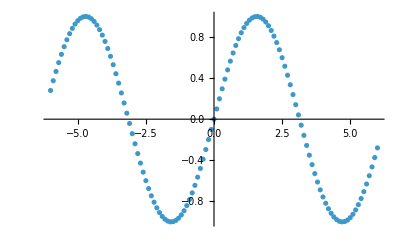

```mathematica
ListPlot[Table[{n, Sin[n]}, {n, -6, 6, 0.1}]]
```

```mathematica
ExampleData[{"TestImage","Couple2"}]
```

-Graphics-

```mathematica
FindTextualAnswer[WikipediaData["Rhinos"], "What the horn of a rhino is made of?"]
```

keratin

```mathematica
Classify["NotablePerson", CurrentImage[]]
```

```mathematica
Entity["Person","FloRida::cyb65"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","FrankOcean::y37b7"]["Image"]
```

-Graphics-

```mathematica
Dataset[EntityValue[Entity["Person","DonaldTrump::6vv3q"],{EntityProperty["Person","FullName"],EntityProperty["Person","BirthDate"],EntityProperty["Person","BirthPlace"]},"PropertyAssociation"]]
```

```mathematica
(#+1)&[9]
```

10

```mathematica
nrst=.
```

```mathematica
nrst:= Nearest[{1,4,6,8,10,15}];
```

```mathematica
nrst[2][[1]]
```

1

```mathematica
nrst[3][[1]]
```

4

```mathematica
Im[3I]
```

3

```mathematica
R[10.2]
```

```mathematica
R[10.2]
```

R[10.2]

```mathematica
√9
```

3

```mathematica
Trace[Plus@@{1,2,3}]
```

{Plus@@{1,2,3},1+2+3,6}

```mathematica
Count[{1,3,5,4, 6.2}, _Integer]
```

4

```mathematica
Take[{1,2,3,4},1]
```

{1}

```mathematica
1//Prime
```

2

```mathematica
Join[{1},{3,4}]
```

{1,3,4}

```mathematica
DeleteDuplicates[{1,3,5,5,4,4, 6.2}]
```

{1,3,5,4,6.2}

```mathematica
PadRight[{1,1,1}, 5, x]
```

{1,1,1,x,x}

```mathematica
Split[{2,2,1,1}]
```

{{2,2},{1,1}}

```mathematica
Outer[f,{1,2},{3,4}]
```

{{f[1,3],f[1,4]},{f[2,3],f[2,4]}}

```mathematica
Partition[{2,2,3,4,5}, 3]
```

{{2,2,3}}

```mathematica
Take[{2,2,3,4,5}, 3]
```

{2,2,3}

```mathematica
Subsets[{2,3,4}]
```

{{},{2},{3},{4},{2,3},{2,4},{3,4},{2,3,4}}

```mathematica
StringPosition["String","Str"][[1]]
```

{1,3}

```mathematica
StringCount["String St r Str2","Str"]
```

2

```mathematica
StringReplace["String", "Str"->"X"]
```

Xing

```mathematica
FreeQ["Str", "Str"]
```

False

```mathematica
Sort[Characters["dcba"]]
```

{a,b,c,d}

```mathematica
DateString[Today]
```

Wed 4 Feb 2026

```mathematica
ToUpperCase["StrinG"]
```

STRING

```mathematica
ToLowerCase["StrinG"]
```

string

```mathematica
CharacterRange["A","Z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
StringMatchQ[" ", WhitespaceCharacter]
```

True

```mathematica
StringSplit["st,rin",","]
```

{st,rin}

```mathematica
StringMatchQ[ToString[x], "x"]
```

True

```mathematica
2^□
```

2^□

```mathematica
2^(2□)
```

```mathematica
2^(2 □2)
```

2^(4 □)

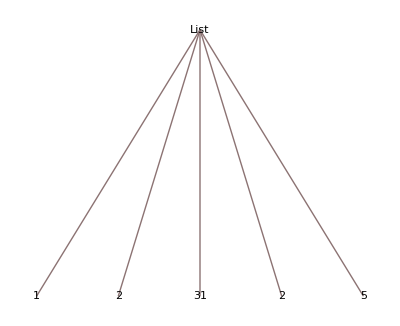

```mathematica
TreeForm[{1,2,31,2,5}]
```

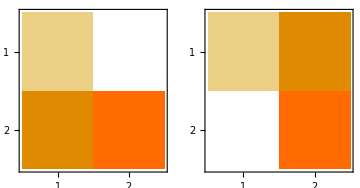

```mathematica
GraphicsRow[{MatrixPlot[{{1,0},{3,4}}],MatrixPlot[Transpose[{{1,0},{3,4}}]]}, ImageSize->Medium]
```

```mathematica
Outer[f,{1,2},{3,4}]
```

{{f[1,3],f[1,4]},{f[2,3],f[2,4]}}

```mathematica
Transpose[{{1,0},{3,4}}][[2]]
```

{0,4}

```mathematica
Transpose[{{1,0},{3,4}}]
```

{{1,3},{0,4}}

```mathematica
TextRecognize[CurrentImage[]]
```

```mathematica
ResourceFunction["StopCamera"]
```

```mathematica
ResourceFunction["StopCamera"][]
```

[]

```mathematica
Transpose[{{1,2,3},{a,b,c}}]
```

{{1,a},{2,b},{3,c}}

```mathematica
(3+#)&[1]
```

4

```mathematica
$LicenseID
```

L4823-8045

```mathematica
$ActivationKey
```

4823-8045-HGYJ6E

```mathematica
TemplateApply["first `a`; second `b`; first `a`",<|"a"->x,"b"->y|>]
```

first x; second y; first x

```mathematica
Interpreter["Chemical"]["Caffeiene"]
```

caffeine

```mathematica
Now
```

Thu 5 Feb 2026 20:00:37GMT

```mathematica
DateString[Now]
```

Thu 5 Feb 2026 20:00:50

```mathematica
DayName[Today]
```

Thursday

```mathematica
MoonPhase[Today, "Icon"]
```

-Graphics-

```mathematica
LocalTime[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
```

Thu 5 Feb 2026 15:05:28GMT-5

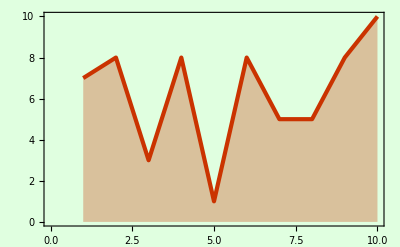

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis,Background->LightGreen]
```

```mathematica
RandomInteger[12,10]
```

{7,0,4,12,9,4,11,2,5,7}

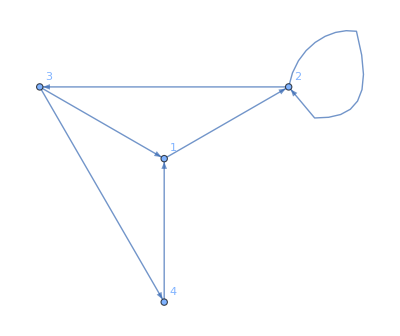
{{{1→2,1→2},{2→3,2→3},{3→4,3→4},{4→1,4→1},{3→1,3→1},{2→2,2→2},{1→2,2→3,3→4,4→1,3→1,2→2}},{VertexLabels→All,VertexLabels→All},{GraphLayout→RadialDrawing,GraphLayout→RadialDrawing},-Graphics-,-Graphics-}

```mathematica
Trace[Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All,GraphLayout->"RadialDrawing"]]
```

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

```mathematica
Classify["Sentiment","math can be really easy?" ]
```

Neutral

```mathematica
Options[Classify ]
```

{AcceptanceThreshold→Automatic,AnomalyDetector→None,BatchProcessing→Automatic,ClassPriors→Automatic,ComputedPropertiesMinSampleNumber→1000,DistributionPostProcessing→Automatic,FeatureExtractor→Identity,FeatureNames→Automatic,FeatureTypes→Automatic,FeatureWeights→Automatic,IndeterminateThreshold→Automatic,Method→Automatic,MissingValueSynthesis→Automatic,NominalVariables→Automatic,PerformanceGoal→Automatic,PredictionName→Automatic,ProcessorCaching→True,RandomSeeding→1234,RecalibrationFunction→Automatic,RecordLog→True,TargetDevice→CPU,TieBreakerFunction→RandomChoice,TimeGoal→Automatic,TrainingProgressCheckpointing→None,TrainingProgressReporting→Automatic,TrainingSizeRatio→Automatic,UtilityFunction→Automatic,ValidationSet→Automatic,Weights→Automatic}

```mathematica
Classify[{-Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 1},
 -Graphics-]
```

1

```mathematica
%299 + 1
```

2

```mathematica
%274
```

{7,0,4,12,9,4,11,2,5,7}

```mathematica
LanguageIdentify["Marhab"]
```

German

```mathematica
FindClusters[{1,2,1,4,a,b, a,c,d}]
```

{{1,1},{a,a},{b},{c},{4},{2},{d}}

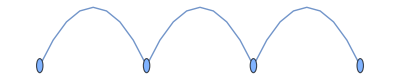

```mathematica
NearestNeighborGraph[{1,2,3,4}, 1]
```

```mathematica
Nearest[WordList[], ToLowerCase["Happ"]]
```

{hap,happy,harp,hasp}

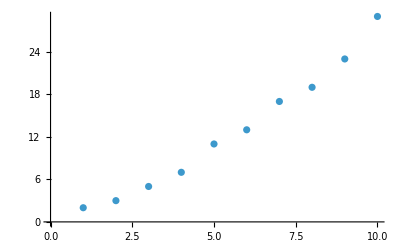

```mathematica
ListPlot[Table[Prime[n],{n,10}]]
```

```mathematica
Fibonacci[4]
```

3

```mathematica
N[100/3,3]
```

33.3

```mathematica
IntegerDigits[655,2]
```

{1,0,1,0,0,0,1,1,1,1}

```mathematica
IntegerDigits[655,10]
```

{6,5,5}

```mathematica
IntegerDigits[655,16]
```

{2,8,15}

```mathematica
x//f
```

f[x]

```mathematica
f@@{x}
```

f[x]

```mathematica
f/@{x}
```

{f[x]}

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[n],{n,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[g[n]],{n,10}]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
a[b[c[d[x]]]]
```

a[b[c[d[x]]]]

```mathematica
x//d//c//b//a
```

a[b[c[d[x]]]]

```mathematica
FullForm[a^b]
```

Power[a,b]

```mathematica
Names["*String"]
```

{ByteArrayToString,ContextToString,DateString,DisplayString,DMSString,EndOfString,ExportString,FromDateString,FrontEndResourceString,FunctionCompileExportString,HighlightString,ImportString,InputString,InString,IntegerString,MemoryUsageInfoString,MissingString,NumberString,ReadString,RepeatedString,SearchQueryString,SemanticImportString,SpokenString,StartOfString,String,TextString,ToString,TypeString,WriteString,$ScriptInputString,$UserAgentString}

```mathematica
points=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

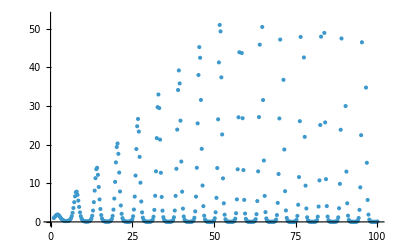

```mathematica
ListPlot[points]
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelingTarget→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotFit→None,PlotFitElements→FitCurve,PlotHighlighting→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
data={{0,18000},{5,10500}};
```

```mathematica
f=LinearModelFit[data,t,t];
```

```mathematica
model = .
```

```mathematica
x = .
```

```mathematica
model=LinearModelFit[Rationalize[data],x,x];
```

```mathematica
myData = Import["/home/shams/Downloads/OA1.2.xlsx", {"Data", 1}]
```

{{X,Y},{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

```mathematica
myData[[All,2;;]]
```

{{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}}

```mathematica
dt1 = Rest[myData]
```

{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

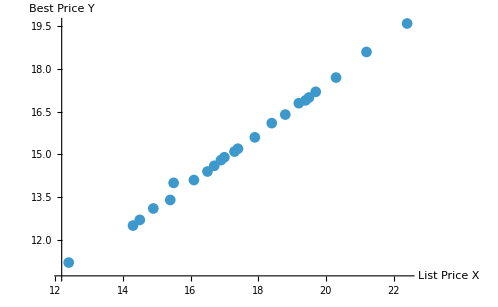

```mathematica
ListPlot[dt1,AxesLabel->{"List Price X","Best Price Y"},PlotMarkers->Automatic]
```

```mathematica
dt = Flatten[myData[[All,2;;]],1]
```

{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

```mathematica
ydt = dt[[;;,2]]
```

{11.2,12.5,12.7,13.1,14.1,14.8,14.4,13.4,14.9,15.6,16.4,17.7,19.6,16.9,14.,14.6,15.1,16.1,16.8,15.2,17.,17.2,18.6}

```mathematica
xdt = dt[[;;,1]]
```

{12.4,14.3,14.5,14.9,16.1,16.9,16.5,15.4,17.,17.9,18.8,20.3,22.4,19.4,15.5,16.7,17.3,18.4,19.2,17.4,19.5,19.7,21.2}

```mathematica
dt
```

{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

```mathematica
LinearModelFit[dt,{1,x},{x}]
```

```mathematica
LinearModelFit[dt,x,x]
```

LinearModelFit::ivar: {1} is not a valid variable.

LinearModelFit[{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}},1,1]

```mathematica
LinearModelFit[dt, x,x]
```

LinearModelFit::ivar: {1} is not a valid variable.

LinearModelFit[{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}},1,1]

```mathematica
Dimensions[xdt]
```

{23}

```mathematica
a=(Max[ydt]-Min[ydt])/(Max[xdt]-Min[xdt])
```

0.84

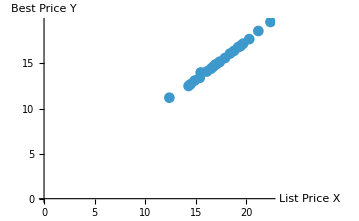

```mathematica
ListPlot[dt,AxesLabel->{"List Price X","Best Price Y"},PlotMarkers->Automatic, AxesOrigin->{0,0}]
```

```mathematica
x=.
```

```mathematica
lm=LinearModelFit[dt,{1,x},x]
```

FittedModel[…]

```mathematica
dt
```

{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

```mathematica
x=.
```

```mathematica
LinearModelFit[dt,{1,x},x]
```

FittedModel[…]

LinearModelFit::notdata: The first argument is not a vector, a matrix or a list containing a design matrix and response vector.

LinearModelFit[data,{1,x},x]

```mathematica
%["BestFit"]
```

0.434584+0.851144 x

```mathematica
knownSlope=0.85;
```

```mathematica
KnownIntcp = -0.4;
```

```mathematica
knownModel[x_]:=knownSlope*x+KnownIntcp
```

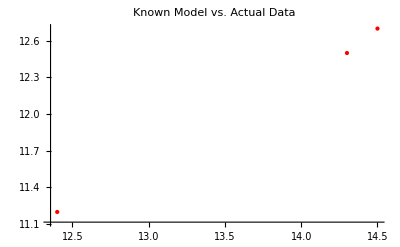

```mathematica
Show[ListPlot[dt,PlotStyle->{Red,PointSize[Medium]}],Plot[knownModel[x],{x,0,5},PlotStyle->Blue],PlotLabel->"Known Model vs. Actual Data"]
```

```mathematica
solution=Solve[model[x]==0,x]
```

{{x→12.}}

```mathematica
model["BestFitParameters"]
```

{18000.,-1500.}

```mathematica
model["BestFitParameters"][[2]]
```

-1500.

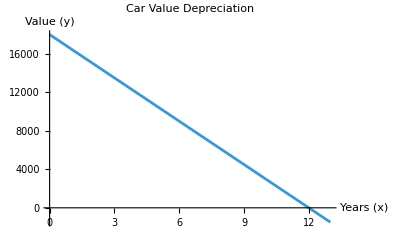

```mathematica
Plot[model[x],{x,0,13},PlotLabel->"Car Value Depreciation",AxesLabel->{"Years (x)","Value (y)"}]
```

```mathematica
pointsPlot=ListPlot[{{0,18000},{5,10500}},PlotStyle->Red];
```

```mathematica
solutionPoint=ListPlot[{{12,0}},PlotStyle->Green,PlotMarkers->{"Disk",10}];
```

Show::gcomb: Could not combine the graphics objects in ….

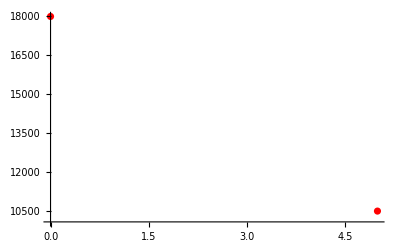
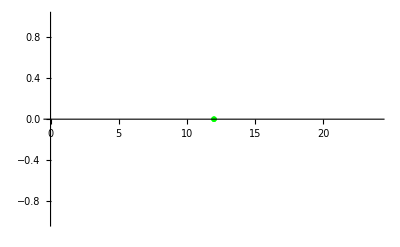
Show[linePlot,-Graphics-,-Graphics-,PlotRange→All,GridLines→{{12},{0}},PlotLabel→Linear Depreciation Solution]

```mathematica
Show[linePlot,pointsPlot,solutionPoint,PlotRange->All,GridLines->{{12},{0}},PlotLabel->"Linear Depreciation Solution"]
```

```mathematica
myData = Import["/home/shams/Downloads/OA1.2.xlsx"]
```

{{{X,Y},{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}}

```mathematica
Total[Flatten[myData, 1][[2;;, 2]]]
```

351.9

```mathematica
Mean[Flatten[myData, 1][[2;;, 1]]]
```

17.4652

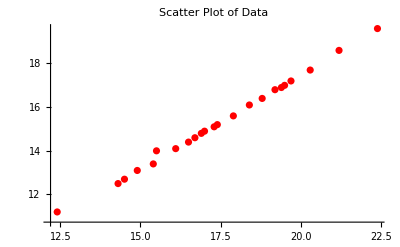

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[myData]

```mathematica
ListPlot[myData,PlotStyle->Red,PlotLabel->"Scatter Plot of Data"]
```

```mathematica
N[1/Sqrt[2], 1000]
```

0.7071067811865475244008443621048490392848359376884740365883398689953662392310535194251937671638207863675069231154561485124624180279253686063220607485499679157066113329637527963778999752505763910302857350547799858029851372672984310073642587093204445993047761646152421543571607254198813018139976257039948436266982731659044148203103076291761975273728751438799808649177876101687659285056771873017042494235801934499853495024075152720138951582271239115342464684593107902892315557983343565065078092844936186176442546324306247488577109167102142843030073412360385717927437077828534838826860113242723507929400810379237461328613001042792233260729199446972185463295900155694123234078541315050297429352001593240171097448639145320522536318440656869927628058661020122545613850113470563786813640247869054483752009184934184225362899682364530381498470690237827411864498590163401237210314634562429526090502229921075295560124720670864265739052901801685538654591434657355085555841958290863444709879358291076064114759244236

```mathematica
Commonest@IntegerDigits@Round[10^1000*]
```

{4}

```mathematica
lst = RealDigits[N[1/Sqrt[2], 1000]][[1]]
```

{7,0,7,1,0,6,7,8,1,1,8,6,5,4,7,5,2,4,4,0,0,8,4,4,3,6,2,1,0,4,8,4,9,0,3,9,2,8,4,8,3,5,9,3,7,6,8,8,4,7,4,0,3,6,5,8,8,3,3,9,8,6,8,9,9,5,3,6,6,2,3,9,2,3,1,0,5,3,5,1,9,4,2,5,1,9,3,7,6,7,1,6,3,8,2,0,7,8,6,3,6,7,5,0,6,9,2,3,1,1,5,4,5,6,1,4,8,5,1,2,4,6,2,4,1,8,0,2,7,9,2,5,3,6,8,6,0,6,3,2,2,0,6,0,7,4,8,5,4,9,9,6,7,9,1,5,7,0,6,6,1,1,3,3,2,9,6,3,7,5,2,7,9,6,3,7,7,8,9,9,9,7,5,2,5,0,5,7,6,3,9,1,0,3,0,2,8,5,7,3,5,0,5,4,7,7,9,9,8,5,8,0,2,9,8,5,1,3,7,2,6,7,2,9,8,4,3,1,0,0,7,3,6,4,2,5,8,7,0,9,3,2,0,4,4,4,5,9,9,3,0,4,7,7,6,1,6,4,6,1,5,2,4,2,1,5,4,3,5,7,1,6,0,7,2,5,4,1,9,8,8,1,3,0,1,8,1,3,9,9,7,6,2,5,7,0,3,9,9,4,8,4,3,6,2,6,6,9,8,2,7,3,1,6,5,9,0,4,4,1,4,8,2,0,3,1,0,3,0,7,6,2,9,1,7,6,1,9,7,5,2,7,3,7,2,8,7,5,1,4,3,8,7,9,9,8,0,8,6,4,9,1,7,7,8,7,6,1,0,1,6,8,7,6,5,9,2,8,5,0,5,6,7,7,1,8,7,3,0,1,7,0,4,2,4,9,4,2,3,5,8,0,1,9,3,4,4,9,9,8,5,3,4,9,5,0,2,4,0,7,5,1,5,2,7,2,0,1,3,8,9,5,1,5,8,2,2,7,1,2,3,9,1,1,5,3,4,2,4,6,4,6,8,4,5,9,3,1,0,7,9,0,2,8,9,2,3,1,5,5,5,7,9,8,3,3,4,3,5,6,5,0,6,5,0,7,8,0,9,2,8,4,4,9,3,6,1,8,6,1,7,6,4,4,2,5,4,6,3,2,4,3,0,6,2,4,7,4,8,8,5,7,7,1,0,9,1,6,7,1,0,2,1,4,2,8,4,3,0,3,0,0,7,3,4,1,2,3,6,0,3,8,5,7,1,7,9,2,7,4,3,7,0,7,7,8,2,8,5,3,4,8,3,8,8,2,6,8,6,0,1,1,3,2,4,2,7,2,3,5,0,7,9,2,9,4,0,0,8,1,0,3,7,9,2,3,7,4,6,1,3,2,8,6,1,3,0,0,1,0,4,2,7,9,2,2,3,3,2,6,0,7,2,9,1,9,9,4,4,6,9,7,2,1,8,5,4,6,3,2,9,5,9,0,0,1,5,5,6,9,4,1,2,3,2,3,4,0,7,8,5,4,1,3,1,5,0,5,0,2,9,7,4,2,9,3,5,2,0,0,1,5,9,3,2,4,0,1,7,1,0,9,7,4,4,8,6,3,9,1,4,5,3,2,0,5,2,2,5,3,6,3,1,8,4,4,0,6,5,6,8,6,9,9,2,7,6,2,8,0,5,8,6,6,1,0,2,0,1,2,2,5,4,5,6,1,3,8,5,0,1,1,3,4,7,0,5,6,3,7,8,6,8,1,3,6,4,0,2,4,7,8,6,9,0,5,4,4,8,3,7,5,2,0,0,9,1,8,4,9,3,4,1,8,4,2,2,5,3,6,2,8,9,9,6,8,2,3,6,4,5,3,0,3,8,1,4,9,8,4,7,0,6,9,0,2,3,7,8,2,7,4,1,1,8,6,4,4,9,8,5,9,0,1,6,3,4,0,1,2,3,7,2,1,0,3,1,4,6,3,4,5,6,2,4,2,9,5,2,6,0,9,0,5,0,2,2,2,9,9,2,1,0,7,5,2,9,5,5,6,0,1,2,4,7,2,0,6,7,0,8,6,4,2,6,5,7,3,9,0,5,2,9,0,1,8,0,1,6,8,5,5,3,8,6,5,4,5,9,1,4,3,4,6,5,7,3,5,5,0,8,5,5,5,5,8,4,1,9,5,8,2,9,0,8,6,3,4,4,4,7,0,9,8,7,9,3,5,8,2,9,1,0,7,6,0,6,4,1,1,4,7,5,9,2,4,4,2,3,6}

```mathematica
MaximalBy[Counts[lst], Identity]
```

<|4→109|>

```mathematica
Reverse@Sort[Counts[lst]]
```

<|4→109,2→108,0→104,3→102,5→102,9→96,1→96,7→96,6→95,8→92|>

```mathematica
Count[lst, 4]
```

109

```mathematica
MaximalBy[Counts[Characters[ExampleData[{"Text","HomerOdysseyGreek"}]]/.Missing[]->Nothing], Identity]
```

<| →87281|>

```mathematica
TextSentences["Human beings. Right.  Rights."][[3]]
```

Rights.

```mathematica
ResourceFunction["TwinPrime"]/@Range[10000]
```

{3,5,7,11,13,17,19,29,31,41,43,59,61,71,73,101,103,107,109,137,139,149,151,179,181,191,193,197,199,227,229,239,241,269,271,281,283,311,313,347,349,419,421,431,433,461,463,521,523,569,571,599,601,617,619,641,643,659,661,809,811,821,823,827,829,857,859,881,883,1019,1021,1031,1033,1049,1051,1061,1063,1091,1093,1151,1153,1229,1231,1277,1279,1289,1291,1301,1303,1319,1321,1427,1429,1451,1453,1481,1483,1487,1489,1607,1609,1619,1621,1667,1669,1697,1699,1721,1723,1787,1789,1871,1873,1877,1879,1931,1933,1949,1951,1997,1999,2027,2029,2081,2083,2087,2089,2111,2113,2129,2131,2141,2143,2237,2239,2267,2269,2309,2311,2339,2341,2381,2383,2549,2551,2591,2593,2657,2659,2687,2689,2711,2713,2729,2731,2789,2791,2801,2803,2969,2971,2999,3001,3119,3121,3167,3169,3251,3253,3257,3259,3299,3301,3329,3331,3359,3361,3371,3373,3389,3391,3461,3463,3467,3469,3527,3529,3539,3541,3557,3559,3581,3583,3671,3673,3767,3769,3821,3823,3851,3853,3917,3919,3929,3931,4001,4003,4019,4021,4049,4051,4091,4093,4127,4129,4157,4159,4217,4219,4229,4231,4241,4243,4259,4261,4271,4273,4337,4339,4421,4423,4481,4483,4517,4519,4547,4549,4637,4639,4649,4651,4721,4723,4787,4789,4799,4801,4931,4933,4967,4969,5009,5011,5021,5023,5099,5101,5231,5233,5279,5281,5417,5419,5441,5443,5477,5479,5501,5503,5519,5521,5639,5641,5651,5653,5657,5659,5741,5743,5849,5851,5867,5869,5879,5881,6089,6091,6131,6133,6197,6199,6269,6271,6299,6301,6359,6361,6449,6451,6551,6553,6569,6571,6659,6661,6689,6691,6701,6703,6761,6763,6779,6781,6791,6793,6827,6829,6869,6871,6947,6949,6959,6961,7127,7129,7211,7213,7307,7309,7331,7333,7349,7351,7457,7459,7487,7489,7547,7549,7559,7561,7589,7591,7757,7759,7877,7879,7949,7951,8009,8011,8087,8089,8219,8221,8231,8233,8291,8293,8387,8389,8429,8431,8537,8539,8597,8599,8627,8629,8819,8821,8837,8839,8861,8863,8969,8971,8999,9001,9011,9013,9041,9043,9239,9241,9281,9283,9341,9343,9419,9421,9431,9433,9437,9439,9461,9463,9629,9631,9677,9679,9719,9721,9767,9769,9857,9859,9929,9931,10007,10009,10037,10039,10067,10069,10091,10093,10139,10141,10271,10273,10301,10303,10331,10333,10427,10429,10457,10459,10499,10501,10529,10531,10709,10711,10859,10861,10889,10891,10937,10939,11057,11059,11069,11071,11117,11119,11159,11161,11171,11173,11351,11353,11489,11491,11549,11551,11699,11701,11717,11719,11777,11779,11831,11833,11939,11941,11969,11971,12041,12043,12071,12073,12107,12109,12161,12163,12239,12241,12251,12253,12377,12379,12539,12541,12611,12613,12821,12823,12917,12919,13001,13003,13007,13009,13217,13219,13337,13339,13397,13399,13679,13681,13691,13693,13709,13711,13721,13723,13757,13759,13829,13831,13877,13879,13901,13903,13931,13933,13997,13999,14009,14011,14081,14083,14249,14251,14321,14323,14387,14389,14447,14449,14549,14551,14561,14563,14591,14593,14627,14629,14867,14869,15137,15139,15269,15271,15287,15289,15329,15331,15359,15361,15581,15583,15641,15643,15647,15649,15731,15733,15737,15739,15887,15889,15971,15973,16061,16063,16067,16069,16139,16141,16187,16189,16229,16231,16361,16363,16451,16453,16631,16633,16649,16651,16691,16693,16829,16831,16901,16903,16979,16981,17027,17029,17189,17191,17207,17209,17291,17293,17387,17389,17417,17419,17489,17491,17579,17581,17597,17599,17657,17659,17681,17683,17747,17749,17789,17791,17837,17839,17909,17911,17921,17923,17957,17959,17987,17989,18041,18043,18047,18049,18059,18061,18119,18121,18131,18133,18251,18253,18287,18289,18311,18313,18521,18523,18539,18541,18911,18913,18917,18919,19079,19081,19139,19141,19181,19183,19211,19213,19379,19381,19421,19423,19427,19429,19469,19471,19541,19543,19697,19699,19751,19753,19841,19843,19889,19891,19961,19963,19991,19993,20021,20023,20147,20149,20231,20233,20357,20359,20441,20443,20477,20479,20507,20509,20549,20551,20639,20641,20717,20719,20747,20749,20771,20773,20807,20809,20897,20899,20981,20983,21011,21013,21017,21019,21059,21061,21191,21193,21317,21319,21377,21379,21491,21493,21521,21523,21557,21559,21587,21589,21599,21601,21611,21613,21647,21649,21737,21739,21839,21841,22037,22039,22091,22093,22109,22111,22157,22159,22271,22273,22277,22279,22367,22369,22481,22483,22541,22543,22571,22573,22619,22621,22637,22639,22697,22699,22739,22741,22859,22861,22961,22963,23027,23029,23039,23041,23057,23059,23201,23203,23291,23293,23369,23371,23537,23539,23561,23563,23627,23629,23669,23671,23687,23689,23741,23743,23831,23833,23909,23911,24107,24109,24179,24181,24371,24373,24419,24421,24917,24919,24977,24979,25031,25033,25169,25171,25301,25303,25307,25309,25409,25411,25469,25471,25577,25579,25601,25603,25799,25801,25847,25849,25931,25933,25997,25999,26111,26113,26249,26251,26261,26263,26681,26683,26699,26701,26711,26713,26729,26731,26861,26863,26879,26881,26891,26893,26951,26953,27059,27061,27107,27109,27239,27241,27281,27283,27407,27409,27479,27481,27527,27529,27539,27541,27581,27583,27689,27691,27737,27739,27749,27751,27791,27793,27917,27919,27941,27943,28097,28099,28109,28111,28181,28183,28277,28279,28307,28309,28349,28351,28409,28411,28547,28549,28571,28573,28619,28621,28661,28663,28751,28753,29021,29023,29129,29131,29207,29209,29387,29389,29399,29401,29567,29569,29669,29671,29759,29761,29879,29881,30011,30013,30089,30091,30137,30139,30269,30271,30389,30391,30467,30469,30491,30493,30557,30559,30839,30841,30851,30853,30869,30871,31079,31081,31121,31123,31151,31153,31181,31183,31247,31249,31319,31321,31391,31393,31511,31513,31541,31543,31721,31723,31727,31729,31769,31771,31847,31849,32027,32029,32057,32059,32117,32119,32141,32143,32189,32191,32297,32299,32321,32323,32369,32371,32411,32413,32441,32443,32531,32533,32561,32563,32609,32611,32717,32719,32801,32803,32831,32833,32909,32911,32939,32941,32969,32971,33071,33073,33149,33151,33179,33181,33287,33289,33329,33331,33347,33349,33587,33589,33599,33601,33617,33619,33749,33751,33767,33769,33809,33811,33827,33829,34031,34033,34127,34129,34157,34159,34211,34213,34259,34261,34301,34303,34367,34369,34469,34471,34499,34501,34511,34513,34589,34591,34649,34651,34757,34759,34841,34843,34847,34849,34961,34963,35051,35053,35081,35083,35279,35281,35447,35449,35507,35509,35531,35533,35591,35593,35729,35731,35801,35803,35837,35839,35897,35899,36011,36013,36107,36109,36341,36343,36467,36469,36527,36529,36779,36781,36791,36793,36899,36901,36929,36931,37019,37021,37199,37201,37307,37309,37337,37339,37361,37363,37547,37549,37571,37573,37589,37591,37691,37693,37781,37783,37811,37813,37991,37993,38237,38239,38327,38329,38447,38449,38459,38461,38567,38569,38609,38611,38651,38653,38669,38671,38711,38713,38747,38749,38921,38923,39041,39043,39161,39163,39227,39229,39239,39241,39341,39343,39371,39373,39509,39511,39827,39829,39839,39841,40037,40039,40127,40129,40151,40153,40427,40429,40529,40531,40637,40639,40697,40699,40847,40849,41141,41143,41177,41179,41201,41203,41231,41233,41387,41389,41411,41413,41519,41521,41609,41611,41759,41761,41849,41851,41957,41959,41981,41983,42017,42019,42071,42073,42179,42181,42221,42223,42281,42283,42407,42409,42461,42463,42569,42571,42641,42643,42701,42703,42839,42841,42899,42901,43049,43051,43319,43321,43397,43399,43541,43543,43577,43579,43607,43609,43649,43651,43781,43783,43787,43789,43889,43891,43961,43963,44027,44029,44087,44089,44129,44131,44201,44203,44267,44269,44279,44281,44381,44383,44531,44533,44621,44623,44699,44701,44771,44773,45119,45121,45137,45139,45179,45181,45317,45319,45341,45343,45587,45589,45821,45823,46049,46051,46091,46093,46181,46183,46271,46273,46307,46309,46349,46351,46439,46441,46589,46591,46679,46681,46769,46771,46817,46819,46829,46831,47057,47059,47147,47149,47351,47353,47387,47389,47417,47419,47657,47659,47699,47701,47711,47713,47741,47743,47777,47779,47807,47809,48119,48121,48311,48313,48407,48409,48479,48481,48539,48541,48647,48649,48677,48679,48731,48733,48779,48781,48821,48823,48857,48859,48869,48871,48989,48991,49031,49033,49121,49123,49169,49171,49199,49201,49277,49279,49331,49333,49367,49369,49391,49393,49409,49411,49529,49531,49547,49549,49667,49669,49739,49741,49787,49789,49919,49921,49937,49939,49991,49993,50021,50023,50051,50053,50129,50131,50261,50263,50459,50461,50549,50551,50591,50593,50891,50893,50969,50971,51059,51061,51131,51133,51197,51199,51239,51241,51341,51343,51347,51349,51419,51421,51437,51439,51479,51481,51719,51721,51767,51769,51827,51829,51869,51871,51971,51973,52067,52069,52181,52183,52289,52291,52361,52363,52541,52543,52709,52711,52859,52861,52901,52903,53087,53089,53147,53149,53171,53173,53231,53233,53267,53269,53279,53281,53549,53551,53591,53593,53609,53611,53717,53719,53897,53899,54011,54013,54401,54403,54419,54421,54497,54499,54539,54541,54581,54583,54629,54631,54917,54919,55049,55051,55217,55219,55331,55333,55337,55339,55439,55441,55619,55621,55631,55633,55661,55663,55817,55819,55901,55903,55931,55933,56039,56041,56099,56101,56207,56209,56237,56239,56267,56269,56477,56479,56501,56503,56531,56533,56597,56599,56711,56713,56807,56809,56891,56893,56909,56911,56921,56923,57191,57193,57221,57223,57269,57271,57329,57331,57347,57349,57527,57529,57557,57559,57791,57793,57899,57901,58109,58111,58151,58153,58169,58171,58229,58231,58367,58369,58391,58393,58439,58441,58451,58453,58601,58603,58787,58789,58907,58909,59009,59011,59021,59023,59051,59053,59207,59209,59219,59221,59357,59359,59417,59419,59441,59443,59471,59473,59627,59629,59669,59671,60089,60091,60101,60103,60167,60169,60257,60259,60647,60649,60659,60661,60761,60763,60887,60889,60899,60901,60917,60919,61151,61153,61331,61333,61379,61381,61469,61471,61559,61561,61979,61981,62129,62131,62141,62143,62189,62191,62297,62299,62927,62929,62969,62971,62981,62983,62987,62989,63029,63031,63197,63199,63311,63313,63389,63391,63419,63421,63587,63589,63599,63601,63647,63649,63689,63691,63839,63841,64151,64153,64187,64189,64301,64303,64451,64453,64577,64579,64661,64663,64781,64783,64877,64879,64919,64921,65027,65029,65099,65101,65171,65173,65267,65269,65447,65449,65519,65521,65537,65539,65579,65581,65699,65701,65717,65719,65729,65731,65837,65839,65927,65929,65981,65983,66107,66109,66359,66361,66569,66571,66749,66751,66851,66853,66947,66949,67139,67141,67187,67189,67211,67213,67217,67219,67271,67273,67409,67411,67427,67429,67577,67579,67757,67759,67931,67933,68111,68113,68207,68209,68279,68281,68447,68449,68489,68491,68711,68713,68819,68821,68879,68881,68897,68899,69029,69031,69149,69151,69191,69193,69257,69259,69401,69403,69491,69493,69497,69499,69737,69739,69761,69763,69827,69829,69857,69859,69929,69931,70001,70003,70121,70123,70139,70141,70181,70183,70199,70201,70379,70381,70457,70459,70487,70489,70571,70573,70619,70621,70841,70843,70877,70879,70919,70921,70949,70951,70979,70981,70997,70999,71261,71263,71327,71329,71339,71341,71387,71389,71411,71413,71471,71473,71549,71551,71711,71713,71807,71809,71879,71881,72089,72091,72101,72103,72167,72169,72221,72223,72227,72229,72251,72253,72269,72271,72467,72469,72647,72649,72671,72673,72869,72871,73037,73039,73061,73063,73361,73363,73607,73609,73679,73681,73847,73849,74099,74101,74159,74161,74201,74203,74381,74383,74411,74413,74507,74509,74609,74611,74717,74719,74729,74731,74759,74761,75011,75013,75167,75169,75209,75211,75389,75391,75401,75403,75539,75541,75617,75619,75707,75709,75989,75991,76001,76003,76079,76081,76157,76159,76259,76261,76367,76369,76421,76423,76541,76543,76649,76651,76829,76831,76871,76873,76961,76963,77237,77239,77261,77263,77267,77269,77417,77419,77477,77479,77489,77491,77549,77551,77687,77689,77711,77713,78137,78139,78191,78193,78437,78439,78509,78511,78539,78541,78569,78571,78779,78781,78887,78889,78977,78979,79151,79153,79229,79231,79397,79399,79559,79561,79631,79633,79691,79693,79697,79699,79811,79813,79841,79843,79901,79903,79997,79999,80147,80149,80207,80209,80231,80233,80447,80449,80471,80473,80489,80491,80627,80629,80669,80671,80681,80683,80747,80749,80777,80779,80831,80833,80909,80911,81017,81019,81041,81043,81047,81049,81197,81199,81281,81283,81371,81373,81551,81553,81647,81649,81701,81703,81899,81901,81929,81931,81971,81973,82007,82009,82037,82039,82139,82141,82217,82219,82349,82351,82469,82471,82529,82531,82559,82561,82721,82723,82727,82729,82757,82759,82811,82813,82889,82891,83219,83221,83231,83233,83267,83269,83339,83341,83399,83401,83561,83563,83639,83641,83717,83719,84059,84061,84179,84181,84221,84223,84317,84319,84347,84349,84389,84391,84521,84523,84629,84631,84809,84811,84857,84859,84869,84871,84977,84979,85091,85093,85199,85201,85331,85333,85361,85363,85427,85429,85451,85453,85619,85621,85667,85669,85817,85819,85829,85831,85931,85933,86027,86029,86111,86113,86291,86293,86351,86353,86369,86371,86531,86533,86627,86629,86927,86929,87011,87013,87119,87121,87149,87151,87179,87181,87221,87223,87251,87253,87509,87511,87539,87541,87557,87559,87587,87589,87629,87631,87641,87643,87719,87721,87959,87961,88001,88003,88259,88261,88337,88339,88469,88471,88589,88591,88607,88609,88661,88663,88799,88801,88811,88813,88817,88819,89069,89071,89519,89521,89561,89563,89597,89599,89657,89659,89669,89671,89819,89821,89897,89899,90017,90019,90071,90073,90197,90199,90371,90373,90401,90403,90437,90439,90527,90529,90617,90619,90677,90679,90821,90823,91079,91081,91097,91099,91127,91129,91139,91141,91151,91153,91367,91369,91457,91459,91571,91573,91811,91813,91967,91969,92177,92179,92219,92221,92381,92383,92399,92401,92459,92461,92567,92569,92639,92641,92669,92671,92681,92683,92789,92791,92861,92863,92957,92959,93131,93133,93239,93241,93251,93253,93281,93283,93479,93481,93491,93493,93557,93559,93701,93703,93761,93763,93809,93811,93887,93889,93911,93913,94007,94009,94109,94111,94151,94153,94307,94309,94349,94351,94397,94399,94439,94441,94529,94531,94541,94543,94559,94561,94649,94651,94847,94849,94949,94951,95087,95089,95189,95191,95231,95233,95441,95443,95789,95791,95801,95803,95957,95959,95987,95989,96179,96181,96221,96223,96329,96331,96587,96589,96737,96739,96797,96799,96821,96823,97001,97003,97157,97159,97169,97171,97301,97303,97367,97369,97379,97381,97499,97501,97547,97549,97577,97579,97607,97609,97649,97651,97787,97789,97841,97843,97847,97849,97859,97861,98009,98011,98297,98299,98321,98323,98387,98389,98561,98563,98639,98641,98711,98713,98729,98731,98807,98809,98867,98869,98897,98899,98909,98911,98927,98929,99131,99133,99137,99139,99257,99259,99347,99349,99527,99529,99707,99709,99719,99721,99989,99991,100151,100153,100361,100363,100391,100393,100517,100519,100547,100549,100799,100801,101111,101113,101117,101119,101159,101161,101207,101209,101279,101281,101501,101503,101531,101533,101747,101749,101837,101839,101999,102001,102059,102061,102077,102079,102101,102103,102197,102199,102251,102253,102299,102301,102407,102409,102497,102499,102677,102679,102761,102763,102911,102913,102929,102931,103067,103069,103091,103093,103289,103291,103391,103393,103421,103423,103811,103813,103841,103843,103967,103969,103979,103981,103991,103993,104087,104089,104147,104149,104231,104233,104309,104311,104381,104383,104471,104473,104549,104551,104681,104683,104759,104761,104801,104803,104849,104851,105227,105229,105251,105253,105359,105361,105527,105529,105767,105769,106031,106033,106121,106123,106187,106189,106217,106219,106277,106279,106319,106321,106451,106453,106541,106543,106619,106621,106661,106663,106751,106753,106781,106783,106859,106861,106961,106963,107069,107071,107099,107101,107507,107509,107717,107719,107837,107839,108011,108013,108107,108109,108191,108193,108287,108289,108377,108379,108461,108463,108497,108499,108707,108709,108791,108793,108881,108883,108947,108949,108959,108961,109139,109141,109169,109171,109199,109201,109451,109453,109469,109471,109517,109519,109619,109621,109661,109663,109829,109831,109841,109843,109847,109849,110321,110323,110477,110479,110501,110503,110567,110569,110729,110731,110819,110821,110879,110881,110921,110923,111029,111031,111119,111121,111227,111229,111269,111271,111491,111493,111731,111733,111779,111781,111827,111829,111869,111871,112067,112069,112247,112249,112289,112291,112337,112339,112361,112363,112571,112573,112601,112603,112757,112759,112919,112921,113021,113023,113039,113041,113081,113083,113147,113149,113159,113161,113171,113173,113327,113329,113357,113359,113381,113383,113537,113539,113621,113623,113717,113719,113759,113761,113777,113779,114041,114043,114197,114199,114599,114601,114641,114643,114659,114661,114689,114691,114797,114799,115019,115021,115151,115153,115301,115303,115319,115321,115361,115363,115469,115471,115601,115603,115769,115771,115781,115783,115859,115861,115877,115879,115901,115903,115931,115933,115979,115981,116099,116101,116189,116191,116531,116533,116537,116539,116687,116689,116789,116791,116927,116929,117041,117043,117191,117193,117239,117241,117329,117331,117371,117373,117497,117499,117539,117541,117617,117619,117671,117673,117701,117703,117809,117811,117839,117841,117881,117883,117977,117979,117989,117991,118169,118171,118211,118213,118247,118249,118409,118411,118619,118621,118799,118801,118901,118903,119087,119089,119099,119101,119129,119131,119291,119293,119297,119299,119417,119419,119549,119551,119657,119659,119687,119689,119699,119701,119771,119773,119849,119851,119921,119923,119981,119983,120047,120049,120077,120079,120689,120691,120737,120739,120917,120919,120941,120943,121019,121021,121061,121063,121169,121171,121349,121351,121367,121369,121439,121441,121577,121579,121607,121609,121631,121633,121787,121789,121949,121951,122027,122029,122039,122041,122051,122053,122147,122149,122201,122203,122207,122209,122321,122323,122387,122389,122399,122401,122501,122503,122597,122599,122609,122611,122651,122653,122741,122743,122867,122869,123377,123379,123491,123493,123551,123553,123581,123583,123731,123733,124121,124123,124181,124183,124247,124249,124301,124303,124337,124339,124349,124351,124427,124429,124541,124543,124769,124771,124781,124783,124907,124909,124979,124981,125117,125119,125219,125221,125507,125509,125639,125641,125789,125791,125897,125899,125927,125929,126011,126013,126227,126229,126491,126493,126611,126613,126857,126859,127031,127033,127079,127081,127217,127219,127247,127249,127289,127291,127607,127609,127679,127681,127709,127711,127817,127819,128111,128113,128201,128203,128237,128239,128339,128341,128411,128413,128519,128521,128549,128551,128657,128659,128747,128749,128831,128833,128939,128941,128969,128971,128981,128983,129119,129121,129221,129223,129287,129289,129401,129403,129497,129499,129527,129529,129587,129589,129629,129631,129641,129643,129917,129919,130199,130201,130259,130261,130367,130369,130409,130411,130619,130621,130631,130633,130649,130651,130841,130843,131009,131011,131111,131113,131249,131251,131447,131449,131477,131479,131639,131641,131711,131713,131777,131779,131837,131839,131891,131893,131939,131941,132047,132049,132329,132331,132437,132439,132527,132529,132707,132709,132749,132751,132761,132763,132857,132859,132947,132949,133277,133279,133319,133321,133349,133351,133541,133543,133631,133633,133709,133711,133811,133813,133979,133981,134087,134089,134291,134293,134339,134341,134369,134371,134399,134401,134591,134593,134681,134683,134837,134839,134921,134923,135017,135019,135209,135211,135281,135283,135347,135349,135389,135391,135431,135433,135461,135463,135467,135469,135599,135601,135647,135649,135719,135721,135911,135913,135977,135979,136067,136069,136397,136399,136481,136483,136601,136603,136649,136651,136691,136693,136709,136711,136751,136753,136811,136813,136859,136861,136949,136951,136991,136993,137087,137089,137117,137119,137339,137341,137867,137869,137909,137911,138077,138079,138179,138181,138239,138241,138371,138373,138401,138403,138449,138451,138569,138571,138797,138799,139121,139123,139199,139201,139301,139303,139367,139369,139457,139459,139589,139591,139661,139663,139967,139969,140069,140071,140417,140419,140549,140551,140627,140629,140681,140683,140729,140731,140759,140761,140837,140839,140867,140869,140891,140893,141179,141181,141221,141223,141497,141499,141509,141511,141677,141679,141707,141709,141767,141769,141851,141853,141959,141961,142097,142099,142157,142159,142589,142591,142607,142609,142697,142699,142757,142759,142787,142789,142871,142873,142979,142981,143111,143113,143261,143263,143501,143503,143567,143569,143651,143653,143831,143833,143879,143881,144071,144073,144161,144163,144167,144169,144407,144409,144479,144481,144539,144541,144887,144889,145007,145009,145511,145513,145547,145549,145601,145603,145679,145681,145721,145723,145757,145759,145931,145933,145967,145969,146009,146011,146021,146023,146057,146059,146297,146299,146381,146383,146519,146521,146681,146683,146891,146893,146987,146989,147029,147031,147137,147139,147209,147211,147227,147229,147449,147451,147671,147673,148061,148063,148151,148153,148199,148201,148301,148303,148469,148471,148667,148669,148691,148693,148721,148723,148781,148783,148859,148861,148931,148933,149057,149059,149099,149101,149111,149113,149159,149161,149249,149251,149417,149419,149489,149491,149519,149521,149531,149533,149561,149563,149627,149629,149711,149713,149729,149731,149837,149839,149909,149911,149969,149971,150089,150091,150209,150211,150221,150223,150299,150301,150377,150379,150587,150589,150767,150769,150881,150883,150959,150961,150989,150991,151007,151009,151049,151051,151169,151171,151241,151243,151337,151339,151379,151381,151607,151609,151769,151771,151847,151849,151901,151903,151937,151939,151967,151969,152027,152029,152039,152041,152081,152083,152417,152419,152441,152443,152459,152461,152531,152533,152597,152599,152639,152641,152819,152821,152837,152839,152897,152899,152939,152941,153071,153073,153269,153271,153407,153409,153509,153511,153521,153523,153887,153889,153911,153913,153947,153949,154079,154081,154157,154159,154181,154183,154211,154213,154277,154279,154571,154573,154589,154591,154619,154621,154667,154669,154787,154789,154871,154873,155081,155083,155201,155203,155381,155383,155537,155539,155579,155581,155717,155719,155849,155851,155861,155863,155891,155893,156059,156061,156227,156229,156257,156259,156419,156421,156491,156493,156677,156679,156797,156799,156899,156901,156941,156943,157049,157051,157217,157219,157229,157231,157271,157273,157277,157279,157349,157351,157427,157429,157559,157561,157637,157639,157667,157669,157769,157771,157931,157933,158141,158143,158231,158233,158357,158359,158747,158749,158759,158761,159167,159169,159191,159193,159347,159349,159539,159541,159569,159571,159629,159631,159671,159673,159737,159739,159791,159793,159869,159871,159977,159979,160031,160033,160079,160081,160091,160093,160481,160483,160619,160621,160637,160639,160649,160651,160709,160711,160751,160753,160877,160879,160967,160969,161339,161341,161459,161461,161561,161563,161639,161641,161729,161731,161741,161743,161771,161773,161879,161881,161921,161923,161969,161971,162287,162289,162389,162391,162527,162529,162749,162751,162821,162823,162971,162973,163019,163021,163061,163063,163127,163129,163169,163171,163307,163309,163409,163411,163481,163483,163859,163861,163979,163981,163991,163993,164147,164149,164231,164233,164249,164251,164429,164431,164447,164449,164621,164623,164837,164839,164999,165001,165047,165049,165311,165313,165551,165553,165587,165589,165701,165703,165707,165709,165719,165721,166301,166303,166349,166351,166601,166603,166667,166669,166739,166741,166781,166783,166841,166843,166847,166849,167021,167023,167117,167119,167267,167269,167309,167311,167339,167341,167441,167443,167621,167623,167777,167779,167861,167863,168449,168451,168599,168601,168629,168631,168899,168901,169007,169009,169067,169069,169217,169219,169241,169243,169319,169321,169691,169693,169751,169753,169889,169891,170099,170101,170351,170353,170369,170371,170537,170539,170759,170761,171047,171049,171077,171079,171161,171163,171167,171169,171251,171253,171401,171403,171467,171469,171539,171541,171671,171673,171761,171763,172169,172171,172217,172219,172421,172423,172439,172441,172517,172519,173021,173023,173189,173191,173207,173209,173291,173293,173357,173359,173429,173431,173669,173671,173741,173743,173777,173779,174017,174019,174047,174049,174077,174079,174257,174259,174329,174331,174467,174469,174569,174571,174761,174763,174929,174931,174989,174991,175067,175069,175079,175081,175391,175393,175631,175633,175757,175759,175781,175783,175937,175939,175961,175963,175991,175993,176021,176023,176051,176053,176087,176089,176159,176161,176327,176329,176417,176419,176459,176461,176507,176509,176549,176551,176597,176599,176609,176611,176711,176713,176777,176779,176789,176791,176807,176809,176921,176923,177011,177013,177209,177211,177431,177433,177677,177679,177761,177763,177839,177841,177887,177889,178037,178039,178067,178069,178091,178093,178247,178249,178259,178261,178349,178351,178439,178441,178487,178489,178559,178561,178601,178603,178691,178693,178817,178819,178907,178909,178931,178933,179381,179383,179579,179581,179591,179593,179657,179659,179687,179689,179717,179719,179819,179821,179897,179899,179951,179953,179999,180001,180071,180073,180179,180181,180239,180241,180287,180289,180539,180541,180749,180751,180797,180799,181001,181003,181061,181063,181199,181201,181211,181213,181301,181303,181397,181399,181457,181459,181499,181501,181607,181609,181667,181669,181757,181759,181787,181789,181871,181873,181889,181891,182009,182011,182027,182029,182057,182059,182099,182101,182129,182131,182177,182179,182339,182341,182387,182389,182471,182473,182639,182641,182657,182659,182711,182713,182927,182929,183089,183091,183299,183301,183317,183319,183437,183439,183497,183499,183509,183511,183569,183571,183707,183709,183761,183763,183917,183919,183971,183973,184187,184189,184271,184273,184487,184489,184607,184609,184631,184633,184649,184651,184829,184831,184901,184903,184967,184969,184997,184999,185069,185071,185369,185371,185531,185533,185567,185569,185681,185683,185747,185749,185819,185821,185831,185833,185957,185959,186161,186163,186227,186229,186299,186301,186377,186379,186479,186481,186581,186583,186647,186649,186707,186709,186761,186763,186869,186871,187067,187069,187127,187129,187139,187141,187217,187219,187337,187339,187469,187471,187631,187633,187637,187639,187907,187909,188831,188833,188861,188863,188939,188941,189017,189019,189041,189043,189149,189151,189251,189253,189347,189349,189389,189391,189437,189439,189491,189493,189617,189619,189797,189799,189851,189853,189947,189949,190367,190369,190577,190579,190667,190669,190709,190711,190889,190891,191141,191143,191249,191251,191297,191299,191339,191341,191447,191449,191459,191461,191507,191509,191531,191533,191561,191563,191669,191671,191747,191749,191801,191803,191831,191833,192191,192193,192317,192319,192341,192343,192461,192463,192497,192499,192581,192583,192611,192613,192629,192631,192887,192889,192977,192979,193181,193183,193379,193381,193601,193603,193811,193813,193859,193861,193871,193873,193937,193939,194069,194071,194267,194269,194681,194683,194861,194863,194867,194869,195047,195049,195161,195163,195341,195343,195539,195541,195731,195733,195737,195739,195929,195931,195971,195973,196169,196171,196277,196279,196499,196501,196541,196543,196661,196663,196769,196771,196871,196873,196991,196993,197159,197161,197297,197299,197339,197341,197369,197371,197381,197383,197567,197569,197597,197599,197711,197713,197891,197893,197957,197959,197969,197971,198221,198223,198257,198259,198347,198349,198437,198439,198461,198463,198827,198829,198839,198841,198899,198901,198941,198943,199037,199039,199151,199153,199487,199489,199499,199501,199601,199603,199739,199741,199751,199753,199811,199813,199931,199933,200381,200383,200867,200869,200927,200929,200987,200989,201119,201121,201209,201211,201401,201403,201449,201451,201491,201493,201497,201499,201767,201769,201821,201823,201827,201829,202061,202063,202127,202129,202289,202291,202637,202639,202751,202753,202877,202879,202931,202933,203207,203209,203309,203311,203321,203323,203339,203341,203351,203353,203381,203383,203417,203419,203429,203431,203459,203461,203657,203659,203771,203773,203807,203809,203909,203911,203969,203971,204161,204163,204299,204301,204329,204331,204359,204361,204437,204439,204509,204511,204599,204601,204749,204751,204791,204793,204857,204859,205031,205033,205211,205213,205397,205399,205421,205423,205661,205663,205949,205951,205991,205993,206081,206083,206177,206179,206249,206251,206279,206281,206411,206413,206639,206641,206819,206821,206909,206911,206951,206953,207197,207199,207239,207241,207329,207331,207341,207343,207479,207481,207509,207511,207521,207523,207671,207673,207719,207721,207797,207799,207971,207973,208001,208003,208139,208141,208277,208279,208391,208393,208457,208459,208499,208501,208511,208513,208589,208591,208697,208699,208889,208891,208931,208933,208961,208963,208991,208993,209201,209203,209267,209269,209357,209359,209567,209569,209579,209581,209621,209623,209717,209719,209819,209821,209927,209929,210191,210193,210317,210319,210359,210361,210401,210403,210599,210601,210809,210811,210911,210913,211049,211051,211061,211063,211151,211153,211217,211219,211229,211231,211499,211501,211571,211573,211661,211663,211691,211693,211877,211879,211889,211891,211931,211933,212207,212209,212669,212671,212867,212869,213131,213133,213287,213289,213359,213361,213611,213613,213947,213949,214007,214009,214031,214033,214211,214213,214481,214483,214517,214519,214559,214561,214787,214789,215141,215143,215351,215353,215459,215461,215687,215689,215981,215983,216317,216319,216371,216373,216551,216553,216569,216571,216647,216649,216779,216781,216899,216901,216917,216919,217001,217003,217199,217201,217307,217309,217337,217339,217361,217363,217367,217369,217409,217411,217517,217519,217559,217561,217577,217579,217907,217909,217979,217981,218081,218083,218417,218419,218459,218461,218549,218551,218627,218629,218717,218719,218969,218971,218987,218989,219017,219019,219311,219313,219407,219409,219647,219649,219677,219679,219761,219763,219797,219799,219941,219943,219977,219979,220019,220021,220469,220471,220511,220513,220859,220861,220877,220879,220901,220903,220931,220933,221069,221071,221171,221173,221201,221203,221399,221401,221411,221413,221537,221539,221621,221623,221657,221659,221717,221719,221951,221953,221987,221989,222041,222043,222107,222109,222149,222151,222161,222163,222197,222199,222347,222349,222791,222793,222839,222841,222977,222979,223007,223009,223049,223051,223061,223063,223217,223219,223241,223243,223337,223339,223439,223441,223547,223549,223679,223681,223757,223759,223829,223831,223841,223843,223919,223921,224069,224071,224129,224131,224909,224911,225077,225079,225161,225163,225221,225223,225287,225289,225341,225343,225347,225349,225371,225373,225527,225529,225581,225583,225611,225613,225749,225751,225767,225769,225779,225781,225941,225943,226199,226201,226379,226381,226451,226453,226547,226549,226817,226819,226901,226903,227111,227113,227189,227191,227231,227233,227471,227473,227531,227533,227567,227569,227609,227611,227627,227629,227651,227653,228197,228199,228299,228301,228419,228421,228509,228511,228521,228523,228617,228619,228731,228733,228797,228799,228881,228883,228911,228913,228959,228961,229247,229249,229547,229549,229589,229591,229637,229639,229751,229753,229769,229771,229847,229849,229937,229939,229961,229963,229979,229981,230309,230311,230339,230341,230387,230389,230561,230563,230771,230773,230861,230863,230939,230941,230999,231001,231017,231019,231107,231109,231269,231271,231347,231349,231431,231433,231461,231463,231479,231481,231611,231613,231821,231823,231839,231841,232049,232051,232079,232081,232187,232189,232409,232411,232457,232459,232709,232711,232751,232753,232961,232963,233069,233071,233141,233143,233159,233161,233327,233329,233417,233419,233549,233551,233687,233689,233879,233881,233921,233923,233939,233941,234191,234193,234317,234319,234341,234343,234461,234463,234527,234529,234539,234541,234587,234589,234809,234811,234959,234961,234977,234979,235007,235009,235241,235243,235307,235309,235439,235441,235661,235663,235787,235789,235811,235813,235889,235891,236207,236209,236477,236479,236699,236701,236771,236773,236867,236869,236879,236881,236891,236893,236981,236983,237071,237073,237089,237091,237161,237163,237689,237691,237857,237859,237971,237973,238037,238039,238079,238081,238157,238159,238361,238363,238529,238531,238727,238729,238877,238879,238919,238921,239231,239233,239387,239389,239429,239431,239711,239713,239849,239851,240041,240043,240047,240049,240257,240259,240347,240349,240587,240589,240881,240883,241049,241051,241067,241069,241259,241261,241361,241363,241391,241393,241511,241513,241559,241561,241601,241603,241781,241783,241919,241921,241979,241981,242057,242059,242171,242173,242447,242449,242519,242521,242729,242731,243119,243121,243401,243403,243431,243433,243587,243589,243671,243673,243701,243703,243707,243709,244157,244159,244217,244219,244301,244303,244379,244381,244637,244639,244667,244669,244841,244843,244859,244861,245129,245131,245171,245173,245417,245419,245471,245473,245519,245521,245561,245563,245591,245593,245627,245629,245681,245683,245849,245851,245897,245899,245909,245911,245981,245983,246119,246121,246131,246133,246317,246319,246509,246511,246611,246613,246641,246643,246707,246709,246809,246811,246929,246931,247067,247069,247337,247339,247391,247393,247529,247531,247601,247603,247607,247609,247649,247651,247691,247693,247769,247771,247811,247813,247991,247993,247997,247999,248117,248119,248177,248179,248201,248203,248291,248293,248639,248641,248867,248869,248891,248893,249131,249133,249419,249421,249437,249439,249497,249499,249539,249541,249857,249859,249971,249973,250049,250051,250499,250501,250739,250741,250751,250753,250949,250951,250967,250969,251057,251059,251177,251179,251201,251203,251219,251221,251231,251233,251261,251263,251429,251431,251609,251611,251621,251623,251789,251791,251831,251833,251939,251941,251969,251971,252827,252829,252911,252913,253157,253159,253367,253369,253607,253609,253637,253639,253679,253681,253787,253789,253907,253909,253949,253951,254039,254041,254207,254209,254279,254281,254489,254491,254729,254731,254831,254833,254927,254929,255179,255181,255191,255193,255251,255253,255467,255469,255587,255589,255839,255841,255917,255919,255971,255973,256019,256021,256031,256033,256187,256189,256391,256393,256469,256471,256577,256579,256721,256723,256799,256801,256901,256903,257219,257221,257351,257353,257399,257401,257501,257503,257687,257689,257711,257713,257861,257863,257867,257869,257987,257989,258107,258109,258317,258319,258329,258331,258611,258613,258917,258919,259121,259123,259157,259159,259211,259213,259379,259381,259451,259453,259619,259621,259781,259783,259991,259993,260009,260011,260189,260191,260207,260209,260411,260413,260417,260419,260549,260551,260807,260809,260861,260863,261011,261013,261059,261061,261167,261169,261431,261433,261641,261643,261971,261973,262049,262051,262109,262111,262151,262153,262349,262351,262511,262513,262541,262543,262649,262651,262739,262741,262781,262783,263267,263269,263399,263401,263489,263491,263519,263521,263609,263611,263759,263761,263819,263821,263867,263869,263909,263911,263951,263953,264029,264031,264137,264139,264167,264169,264527,264529,264599,264601,264791,264793,264827,264829,264959,264961,265091,265093,265247,265249,265271,265273,265337,265339,265511,265513,265541,265543,265619,265621,265709,265711,265871,265873,266027,266029,266051,266053,266081,266083,266291,266293,266351,266353,266447,266449,266477,266479,266489,266491,266681,266683,266687,266689,266837,266839,266897,266899,267131,267133,267227,267229,267299,267301,267389,267391,267401,267403,267431,267433,267479,267481,267521,267523,267611,267613,267647,267649,267677,267679,267719,267721,267737,267739,267899,267901,267959,267961,268517,268519,268529,268531,268757,268759,268781,268783,268811,268813,268817,268819,268841,268843,268997,268999,269039,269041,269177,269179,269219,269221,269387,269389,269429,269431,270029,270031,270071,270073,270131,270133,270239,270241,270269,270271,270461,270463,270551,270553,270761,270763,270797,270799,271127,271129,271277,271279,271499,271501,271571,271573,271637,271639,271769,271771,271967,271969,272009,272011,272189,272191,272201,272203,272267,272269,272351,272353,272381,272383,272537,272539,272717,272719,272759,272761,272807,272809,272981,272983,272999,273001,273059,273061,273269,273271,273281,273283,273311,273313,273641,273643,273899,273901,273941,273943,274121,274123,274199,274201,274451,274453,274709,274711,274829,274831,275129,275131,275159,275161,275321,275323,275447,275449,275459,275461,275489,275491,275579,275581,275591,275593,275921,275923,275939,275941,276041,276043,276047,276049,276371,276373,276587,276589,276671,276673,276779,276781,276821,276823,276917,276919,277097,277099,277259,277261,277427,277429,277547,277549,277577,277579,277601,277603,277637,277639,277787,277789,277889,277891,278147,278149,278207,278209,278489,278491,278501,278503,278561,278563,278609,278611,278687,278689,278741,278743,278807,278809,278879,278881,278909,278911,279119,279121,279479,279481,279551,279553,279707,279709,280097,280099,280337,280339,280409,280411,280547,280549,280589,280591,280697,280699,280769,280771,281189,281191,281249,281251,281429,281431,281549,281551,281579,281581,281621,281623,281651,281653,281717,281719,281837,281839,281921,281923,282089,282091,282101,282103,282239,282241,282311,282313,282389,282391,282407,282409,282677,282679,282767,282769,282911,282913,283007,283009,283097,283099,283181,283183,283487,283489,283571,283573,283607,283609,283637,283639,283769,283771,283859,283861,284057,284059,284129,284131,284159,284161,284231,284233,284267,284269,284507,284509,284591,284593,284657,284659,284729,284731,284741,284743,284747,284749,284831,284833,284897,284899,285119,285121,285281,285283,285287,285289,285557,285559,285611,285613,285629,285631,285641,285643,285707,285709,285839,285841,285977,285979,286061,286063,286367,286369,286457,286459,286541,286543,286589,286591,286751,286753,287057,287059,287237,287239,287279,287281,287501,287503,287669,287671,287849,287851,288179,288181,288359,288361,288527,288529,288647,288649,288731,288733,288851,288853,288929,288931,288989,288991,289019,289021,289031,289033,289109,289111,289127,289129,289139,289141,289169,289171,289241,289243,289841,289843,290021,290023,290039,290041,290441,290443,290471,290473,290531,290533,290621,290623,290657,290659,290669,290671,290837,290839,291041,291043,291101,291103,291167,291169,291371,291373,291437,291439,291647,291649,291689,291691,291899,291901,292079,292081,292091,292093,292181,292183,292469,292471,292709,292711,293147,293149,293177,293179,293261,293263,293861,293863,293999,294001,294167,294169,294179,294181,294311,294313,294317,294319,294647,294649,294947,294949,294989,294991,295037,295039,295079,295081,295199,295201,295439,295441,295871,295873,295877,295879,295901,295903,295949,295951,296249,296251,296477,296479,296507,296509,296561,296563,296579,296581,296729,296731,296771,296773,296831,296833,296909,296911,296969,296971,296981,296983,297467,297469,297809,297811,297989,297991,298157,298159,298169,298171,298211,298213,298409,298411,298679,298681,298691,298693,298757,298759,298799,298801,298817,298819,299027,299029,299357,299359,299417,299419,299471,299473,299477,299479,299567,299569,299681,299683,299699,299701,300149,300151,300191,300193,300299,300301,300317,300319,300491,300493,300497,300499,300581,300583,300647,300649,300719,300721,300821,300823,300929,300931,301181,301183,301241,301243,301331,301333,301361,301363,301487,301489,301577,301579,301751,301753,301841,301843,301991,301993,301997,301999,302171,302173,302189,302191,302297,302299,302579,302581,302831,302833,302969,302971,303011,303013,303089,303091,303377,303379,303491,303493,303551,303553,303617,303619,303647,303649,303689,303691,304067,304069,304151,304153,304301,304303,304391,304393,304457,304459,304559,304561,304847,304849,304901,304903,304979,304981,305021,305023,305111,305113,305351,305353,305411,305413,305477,305479,305717,305719,305741,305743,305759,305761,306167,306169,306191,306193,306329,306331,306347,306349,306419,306421,306587,306589,306701,306703,306827,306829,306947,306949,307031,307033,307091,307093,307169,307171,307187,307189,307259,307261,307337,307339,307397,307399,307631,307633,307691,307693,307871,307873,308291,308293,308309,308311,308489,308491,308507,308509,308519,308521,308639,308641,308849,308851,308927,308929,309011,309013,309107,309109,309269,309271,309311,309313,309479,309481,309521,309523,309539,309541,309779,309781,309851,309853,309929,309931,310019,310021,310127,310129,310229,310231,310361,310363,310727,310729,310829,310831,311291,311293,311537,311539,311567,311569,311681,311683,311711,311713,311747,311749,311867,311869,312029,312031,312071,312073,312197,312199,312209,312211,312251,312253,312281,312283,312311,312313,312551,312553,312581,312583,312617,312619,312677,312679,312701,312703,312839,312841,312929,312931,312941,312943,313127,313129,313151,313153,313331,313333,313637,313639,313739,313741,313931,313933,313979,313981,313991,313993,314159,314161,314261,314263,314357,314359,314399,314401,314597,314599,314777,314779,315011,315013,315179,315181,315407,315409,315449,315451,315527,315529,315701,315703,315881,315883,316031,316033,316241,316243,316469,316471,316499,316501,316661,316663,316697,316699,316817,316819,316859,316861,317087,317089,317267,317269,317321,317323,317351,317353,317489,317491,317591,317593,317729,317731,317741,317743,317771,317773,317921,317923,317957,317959,317969,317971,318179,318181,318209,318211,318287,318289,318299,318301,318347,318349,318557,318559,318677,318679,318749,318751,318809,318811,318881,318883,318917,318919,319127,319129,319439,319441,319589,319591,319679,319681,319727,319729,319817,319819,319829,319831,320009,320011,320039,320041,320081,320083,320141,320143,320237,320239,320267,320269,320291,320293,320387,320389,320561,320563,320609,320611,320657,320659,320939,320941,321311,321313,321329,321331,321467,321469,321569,321571,321617,321619,321707,321709,321821,321823,321947,321949,322037,322039,322109,322111,322169,322171,322247,322249,322349,322351,322571,322573,322589,322591,322631,322633,322769,322771,322781,322783,322919,322921,322997,322999,323249,323251,323339,323341,323369,323371,323381,323383,323441,323443,323471,323473,323507,323509,323579,323581,323597,323599,323801,323803,324209,324211,324299,324301,324437,324439,324449,324451,324587,324589,324617,324619,324809,324811,324869,324871,324977,324979,325019,325021,325079,325081,325187,325189,325217,325219,325229,325231,325307,325309,325541,325543,325691,325693,325751,325753,325781,325783,325889,325891,326099,326101,326141,326143,326147,326149,326351,326353,326537,326539,326561,326563,326609,326611,326657,326659,326867,326869,326939,326941,326999,327001,327209,327211,327317,327319,327407,327409,327419,327421,327491,327493,327557,327559,327581,327583,327737,327739,327797,327799,327827,327829,327851,327853,327869,327871,328061,328063,328127,328129,328331,328333,328379,328381,328511,328513,328589,328591,328619,328621,328637,328639,328787,328789,328847,328849,328919,328921,329081,329083,329207,329209,329267,329269,329297,329299,329471,329473,329627,329629,329801,329803,330017,330019,330131,330133,330227,330229,330287,330289,330311,330313,330329,330331,330431,330433,330641,330643,330719,330721,330791,330793,330821,330823,330857,330859,331337,331339,331367,331369,331547,331549,331577,331579,331691,331693,331841,331843,331907,331909,331997,331999,332009,332011,332159,332161,332201,332203,332219,332221,332471,332473,332567,332569,332987,332989,333029,333031,333101,333103,333269,333271,333449,333451,333491,333493,333719,333721,333791,333793,334331,334333,334421,334423,334427,334429,334511,334513,334547,334549,334751,334753,334889,334891,334991,334993,335171,335173,335381,335383,335807,335809,336029,336031,336101,336103,336221,336223,336251,336253,336527,336529,336767,336769,336827,336829,336899,336901,337217,337219,337277,337279,337367,337369,337487,337489,337541,337543,337607,337609,337859,337861,337871,337873,337901,337903,338159,338161,338267,338269,338321,338323,338339,338341,338411,338413,338579,338581,339137,339139,339671,339673,339749,339751,339839,339841,340061,340063,340127,340129,340337,340339,340451,340453,340577,340579,340787,340789,340931,340933,340937,340939,341057,341059,341321,341323,341459,341461,341771,341773,341951,341953,342047,342049,342059,342061,342071,342073,342239,342241,342281,342283,342341,342343,342371,342373,342449,342451,342467,342469,342869,342871,343307,343309,343379,343381,343391,343393,343529,343531,343559,343561,343589,343591,343769,343771,343799,343801,343829,343831,344171,344173,344207,344209,344249,344251,344291,344293,344681,344683,344819,344821,344957,344959,345017,345019,345227,345229,345461,345463,345599,345601,345731,345733,345887,345889,346139,346141,346259,346261,346391,346393,346397,346399,346439,346441,346559,346561,346649,346651,346667,346669,346961,346963,347057,347059,347069,347071,347129,347131,347141,347143,347297,347299,347561,347563,347729,347731,347771,347773,347957,347959,347981,347983,347987,347989,348239,348241,348419,348421,348431,348433,348461,348463,348917,348919,348989,348991,349079,349081,349379,349381,349397,349399,349409,349411,349829,349831,349931,349933,350087,350089,350429,350431,350561,350563,350729,350731,350981,350983,351059,351061,351077,351079,351257,351259,351287,351289,351341,351343,351359,351361,351731,351733,351749,351751,351929,351931,352109,352111,352271,352273,352367,352369,352409,352411,352421,352423,352481,352483,352739,352741,352817,352819,352907,352909,352949,352951,353147,353149,353201,353203,353471,353473,353627,353629,353867,353869,354041,354043,354251,354253,354257,354259,354371,354373,354461,354463,354551,354553,354701,354703,354881,354883,354971,354973,355007,355009,355037,355039,355109,355111,355361,355363,355499,355501,355517,355519,355571,355573,355721,355723,355937,355939,355967,355969,356141,356143,356171,356173,356261,356263,356441,356443,356561,356563,356819,356821,356927,356929,357107,357109,357197,357199,357239,357241,357281,357283,357347,357349,357569,357571,357611,357613,357659,357661,357737,357739,357779,357781,358157,358159,358277,358279,358289,358291,358427,358429,358571,358573,358667,358669,358859,358861,358877,358879,358901,358903,358907,358909,359207,359209,359297,359299,359417,359419,359477,359479,359561,359563,360089,360091,360167,360169,360287,360289,360509,360511,360779,360781,360821,360823,360851,360853,360947,360949,360977,360979,361001,361003,361091,361093,361211,361213,361217,361219,361349,361351,361409,361411,361649,361651,361787,361789,361871,361873,361901,361903,362051,362053,362291,362293,362429,362431,362741,362743,362951,362953,363017,363019,363059,363061,363149,363151,363269,363271,363359,363361,363371,363373,363401,363403,363437,363439,363887,363889,363947,363949,364127,364129,364289,364291,364541,364543,364751,364753,364919,364921,365249,365251,365291,365293,365411,365413,365471,365473,365507,365509,365567,365569,365639,365641,365747,365749,365837,365839,366029,366031,366167,366169,366341,366343,366437,366439,366461,366463,366701,366703,366851,366853,367019,367021,367121,367123,367229,367231,367259,367261,367307,367309,367559,367561,367649,367651,368231,368233,368651,368653,368789,368791,368801,368803,369077,369079,369407,369409,369659,369661,369791,369793,369827,369829,369959,369961,370421,370423,370439,370441,370661,370663,370871,370873,371027,371029,371069,371071,371141,371143,371177,371179,371249,371251,371339,371341,371387,371389,371927,371929,371939,371941,372059,372061,372269,372271,372311,372313,372611,372613,372707,372709,372941,372943,372971,372973,373181,373183,373211,373213,373229,373231,373361,373363,373487,373489,373859,373861,374039,374041,374291,374293,374441,374443,374639,374641,374681,374683,374837,374839,374987,374989,375017,375019,375101,375103,375119,375121,375251,375253,375257,375259,375281,375283,375371,375373,375449,375451,375509,375511,375707,375709,375899,375901,376001,376003,376097,376099,376469,376471,376529,376531,376631,376633,376757,376759,376889,376891,376931,376933,377171,377173,377327,377329,377369,377371,377561,377563,378149,378151,378239,378241,378569,378571,378821,378823,379007,379009,379187,379189,379397,379399,379439,379441,379499,379501,379571,379573,379679,379681,379721,379723,379997,379999,380129,380131,380201,380203,380267,380269,380309,380311,380327,380329,380459,380461,380621,380623,380837,380839,380867,380869,380879,380881,381167,381169,381221,381223,381287,381289,381371,381373,381527,381529,381629,381631,381737,381739,381791,381793,381989,381991,382001,382003,382229,382231,382427,382429,382661,382663,382727,382729,382871,382873,383081,383083,383099,383101,383219,383221,383417,383419,383519,383521,383609,383611,383657,383659,383681,383683,383837,383839,384257,384259,384287,384289,384299,384301,384479,384481,385079,385081,385127,385129,385139,385141,385289,385291,385391,385393,385571,385573,385589,385591,385661,385663,385739,385741,386039,386041,386117,386119,386129,386131,386159,386161,386297,386299,386369,386371,386381,386383,386411,386413,386429,386431,386609,386611,386987,386989,387197,387199,387677,387679,387911,387913,387971,387973,388109,388111,388181,388183,388481,388483,388691,388693,388697,388699,388901,388903,388931,388933,388961,388963,389027,389029,389171,389173,389297,389299,389399,389401,389531,389533,389561,389563,389567,389569,389999,390001,390107,390109,390191,390193,390209,390211,390389,390391,390419,390421,390491,390493,390671,390673,390737,390739,390959,390961,390989,390991,391019,391021,391217,391219,391247,391249,391397,391399,391451,391453,391691,391693,391751,391753,391889,391891,392099,392101,392111,392113,392261,392263,392267,392269,392279,392281,392297,392299,392759,392761,392807,392809,392849,392851,392927,392929,392981,392983,393077,393079,393299,393301,393401,393403,393539,393541,393581,393583,393857,393859,393929,393931,394367,394369,394409,394411,394577,394579,394631,394633,394727,394729,394811,394813,394817,394819,394967,394969,395111,395113,395189,395191,395321,395323,395429,395431,395849,395851,396029,396031,396041,396043,396197,396199,396299,396301,396377,396379,396629,396631,396881,396883,397151,397153,397181,397183,397301,397303,397427,397429,397517,397519,397541,397543,397547,397549,397589,397591,397721,397723,397751,397753,397757,397759,398117,398119,398339,398341,398471,398473,398609,398611,398681,398683,398729,398731,398819,398821,399149,399151,399239,399241,399281,399283,399389,399391,399401,399403,399491,399493,399689,399691,399851,399853,399911,399913,400031,400033,400067,400069,400247,400249,400679,400681,400721,400723,401309,401311,401537,401539,401627,401629,401669,401671,401771,401773,401957,401959,402089,402091,402131,402133,402137,402139,402221,402223,402329,402331,402341,402343,402359,402361,402527,402529,402581,402583,402761,402763,402767,402769,402947,402949,403001,403003,403061,403063,403241,403243,403547,403549,403679,403681,403829,403831,403979,403981,404009,404011,404189,404191,404249,404251,404267,404269,404321,404323,404387,404389,404429,404431,404531,404533,404849,404851,404981,404983,405047,405049,405071,405073,405089,405091,405239,405241,405341,405343,405437,405439,405497,405499,405527,405529,405677,405679,405701,405703,405827,405829,405869,405871,405947,405949,405989,405991,406169,406171,406499,406501,406559,406561,406577,406579,406631,406633,406697,406699,407177,407179,407219,407221,407357,407359,407501,407503,407789,407791,407969,407971,408209,408211,408431,408433,408689,408691,408701,408703,408911,408913,409259,409261,409289,409291,409349,409351,409691,409693,409709,409711,409889,409891,410117,410119,410141,410143,410171,410173,410231,410233,410279,410281,410339,410341,410411,410413,410489,410491,410621,410623,410747,410749,410999,411001,411011,411013,411251,411253,411527,411529,411611,411613,411707,411709,411737,411739,411821,411823,412031,412033,412037,412039,412187,412189,412211,412213,412589,412591,412637,412639,412901,412903,413069,413071,413087,413089,413111,413113,413141,413143,413681,413683,413711,413713,413867,413869,414017,414019,414107,414109,414311,414313,414329,414331,414431,414433,414641,414643,414677,414679,414707,414709,414767,414769,415109,415111,415187,415189,415271,415273,415379,415381,415607,415609,415799,415801,415949,415951,416147,416149,416387,416389,416399,416401,416417,416419,416441,416443,416501,416503,416621,416623,416849,416851,417017,417019,417377,417379,417491,417493,417509,417511,417581,417583,417719,417721,417731,417733,417881,417883,417959,417961,418007,418009,418337,418339,418349,418351,418601,418603,418631,418633,418811,418813,419051,419053,419057,419059,419189,419191,419561,419563,419597,419599,419789,419791,419801,419803,419927,419929,419999,420001,420191,420193,420269,420271,420317,420319,420419,420421,420479,420481,420569,420571,420779,420781,420809,420811,420851,420853,420857,420859,421079,421081,421121,421123,421469,421471,421607,421609,421697,421699,421709,421711,421739,421741,422087,422089,422099,422101,422111,422113,422309,422311,422549,422551,422759,422761,422867,422869,422879,422881,422897,422899,423257,423259,423287,423289,423461,423463,423557,423559,423749,423751,423779,423781,423989,423991,424001,424003,424091,424093,424271,424273,424547,424549,424727,424729,424769,424771,424817,424819,424841,424843,424889,424891,425057,425059,425147,425149,425279,425281,425417,425419,425441,425443,425471,425473,425519,425521,425837,425839,425987,425989,426089,426091,426161,426163,426551,426553,426707,426709,426737,426739,426761,426763,426917,426919,426971,426973,427067,427069,427079,427081,427241,427243,427247,427249,427307,427309,427379,427381,427421,427423,427619,427621,427787,427789,427877,427879,427949,427951,427967,427969,427991,427993,428039,428041,428147,428149,428249,428251,428297,428299,428471,428473,428567,428569,428807,428809,429137,429139,429281,429283,429347,429349,429467,429469,429509,429511,429587,429589,429659,429661,429677,429679,429731,429733,429851,429853,429887,429889,429899,429901,429929,429931,429971,429973,430007,430009,430091,430093,430277,430279,430511,430513,430601,430603,430697,430699,430739,430741,430751,430753,430907,430909,430979,430981,431267,431269,431447,431449,431657,431659,431729,431731,431801,431803,431831,431833,431867,431869,432137,432139,432161,432163,432389,432391,432557,432559,432587,432589,432659,432661,432797,432799,432959,432961,433049,433051,433259,433261,433469,433471,433661,433663,433679,433681,433859,433861,434009,434011,434111,434113,434387,434389,434459,434461,434561,434563,434717,434719,434921,434923,435107,435109,435179,435181,435221,435223,435401,435403,435437,435439,435569,435571,435647,435649,435731,435733,435857,435859,435947,435949,436307,436309,436481,436483,436529,436531,436547,436549,436649,436651,436727,436729,436739,436741,437111,437113,437387,437389,437471,437473,437651,437653,438047,438049,438131,438133,438521,438523,438827,438829,439007,439009,439427,439429,440177,440179,440441,440443,440507,440509,440549,440551,440567,440569,440579,440581,440651,440653,440681,440683,440807,440809,440939,440941,440987,440989,441041,441043,441107,441109,441191,441193,441359,441361,441797,441799,441827,441829,441839,441841,442007,442009,442031,442033,442397,442399,442487,442489,442499,442501,442571,442573,442577,442579,442829,442831,442961,442963,443039,443041,443057,443059,443159,443161,443291,443293,443561,443563,443687,443689,443759,443761,443867,443869,443879,443881,443939,443941,443999,444001,444179,444181,444287,444289,444341,444343,444347,444349,444401,444403,444461,444463,444527,444529,444791,444793,445019,445021,445031,445033,445631,445633,445769,445771,445967,445969,446189,446191,446261,446263,446387,446389,446399,446401,446891,446893,446909,446911,447257,447259,447449,447451,447569,447571,447701,447703,447791,447793,447827,447829,448139,448141,448157,448159,448631,448633,448871,448873,448997,448999,449129,449131,449171,449173,449201,449203,449261,449263,449417,449419,449567,449569,449987,449989,450101,450103,450257,450259,450299,450301,450479,450481,450599,450601,450641,450643,450797,450799,450809,450811,450839,450841,450881,450883,451181,451183,451277,451279,451301,451303,451439,451441,451667,451669,451679,451681,451901,451903,451937,451939,452159,452161,452519,452521,452531,452533,452537,452539,452687,452689,453197,453199,453377,453379,453569,453571,453599,453601,453641,453643,453707,453709,453797,453799,454031,454033,454061,454063,454211,454213,454229,454231,454451,454453,454541,454543,454577,454579,454709,454711,454721,454723,454847,454849,454889,454891,454919,454921,454967,454969,455261,455263,455339,455341,455471,455473,455489,455491,455597,455599,455681,455683,456107,456109,456149,456151,456557,456559,456611,456613,456647,456649,456767,456769,456809,456811,456899,456901,457001,457003,457097,457099,457151,457153,457277,457279,457397,457399,457607,457609,457979,457981,458189,458191,458399,458401,458531,458533,458567,458569,458789,458791,458957,458959,459029,459031,459089,459091,459167,459169,459341,459343,459467,459469,459521,459523,459647,459649,460079,460081,460709,460711,460841,460843,460949,460951,460979,460981,461009,461011,461051,461053,461297,461299,461411,461413,461441,461443,461687,461689,461801,461803,462419,462421,462491,462493,462569,462571,462641,462643,462899,462901,463031,463033,463247,463249,463319,463321,463451,463453,463457,463459,463511,463513,463829,463831,463889,463891,463919,463921,464129,464131,464141,464143,464171,464173,464279,464281,464309,464311,464381,464383,464537,464539,464747,464749,464771,464773,464801,464803,464939,464941,464951,464953,465011,465013,465077,465079,465161,465163,465167,465169,465209,465211,465317,465319,465797,465799,465929,465931,466181,466183,466649,466651,467081,467083,467237,467239,467471,467473,467477,467479,467627,467629,467669,467671,467867,467869,467879,467881,467897,467899,468107,468109,468239,468241,468491,468493,468737,468739,468887,468889,469367,469369,469541,469543,469877,469879,470081,470083,470087,470089,470207,470209,470297,470299,470411,470413,470471,470473,470597,470599,470651,470653,470957,470959,471089,471091,471137,471139,471281,471283,471299,471301,471389,471391,471617,471619,471671,471673,471719,471721,471929,471931,472247,472249,472331,472333,472391,472393,472541,472543,472559,472561,472709,472711,472907,472909,472937,472939,473201,473203,473351,473353,473381,473383,473441,473443,473477,473479,473531,473533,473741,473743,473927,473929,473951,473953,474389,474391,474497,474499,474569,474571,474581,474583,474707,474709,474809,474811,475091,475093,475271,475273,475331,475333,475367,475369,475379,475381,475427,475429,475619,475621,475637,475639,475679,475681,475691,475693,475751,475753,475877,475879,476027,476029,476039,476041,476087,476089,476477,476479,476681,476683,476849,476851,477011,477013,477017,477019,477359,477361,477551,477553,477767,477769,477809,477811,477821,477823,478067,478069,478169,478171,478241,478243,478271,478273,478451,478453,478481,478483,478571,478573,478727,478729,478739,478741,478811,478813,479027,479029,479189,479191,479429,479431,479879,479881,479951,479953,480017,480019,480047,480049,480059,480061,480167,480169,480341,480343,480449,480451,480461,480463,481001,481003,481301,481303,481697,481699,481751,481753,481847,481849,482099,482101,482231,482233,482399,482401,482507,482509,482687,482689,482717,482719,482861,482863,482897,482899,483209,483211,483407,483409,483809,483811,483827,483829,484151,484153,484301,484303,484457,484459,484487,484489,484607,484609,485207,485209,485729,485731,485831,485833,486041,486043,486179,486181,486221,486223,486329,486331,486377,486379,486389,486391,486509,486511,486641,486643,486677,486679,486767,486769,486947,486949,487049,487051,487211,487213,487427,487429,487469,487471,487601,487603,487649,487651,487829,487831,487889,487891,488009,488011,488207,488209,488231,488233,488261,488263,488309,488311,488399,488401,488417,488419,488639,488641,488687,488689,489239,489241,489407,489409,489551,489553,489677,489679,489689,489691,489791,489793,489869,489871,489911,489913,489941,489943,489959,489961,490001,490003,490031,490033,490247,490249,490541,490543,490571,490573,490577,490579,490661,490663,490769,490771,490949,490951,490967,490969,490991,490993,491039,491041,491081,491083,491297,491299,491327,491329,491339,491341,491501,491503,491537,491539,491591,491593,491651,491653,492059,492061,492251,492253,492617,492619,492629,492631,492671,492673,492719,492721,492761,492763,493109,493111,493121,493123,493217,493219,493277,493279,493397,493399,493709,493711,493811,493813,493937,493939,494267,494269,494381,494383,494441,494443,494519,494521,494561,494563,494759,494761,495041,495043,495149,495151,495359,495361,495557,495559,495569,495571,495587,495589,495611,495613,495617,495619,495749,495751,495797,495799,495827,495829,496229,496231,496289,496291,496889,496891,496997,496999,497111,497113,497279,497281,497507,497509,497771,497773,497867,497869,498101,498103,498257,498259,498401,498403,498467,498469,498521,498523,498611,498613,498689,498691,498779,498781,498857,498859,499127,499129,499139,499141,499157,499159,499181,499183,499361,499363,499481,499483,499661,499663,499691,499693,500111,500113,500177,500179,500231,500233,500237,500239,500471,500473,500807,500809,500909,500911,500921,500923,501029,501031,501131,501133,501341,501343,501701,501703,501827,501829,502079,502081,502259,502261,502499,502501,502631,502633,502769,502771,502919,502921,503231,503233,503381,503383,503549,503551,503609,503611,503621,503623,503777,503779,503819,503821,503927,503929,504149,504151,504377,504379,504521,504523,504617,504619,504797,504799,504851,504853,504989,504991,505031,505033,505049,505051,505157,505159,505277,505279,505319,505321,505367,505369,505409,505411,505511,505513,505691,505693,505709,505711,506171,506173,506327,506329,506459,506461,506531,506533,506591,506593,506687,506689,506729,506731,507077,507079,507137,507139,507149,507151,507347,507349,507359,507361,507497,507499,507779,507781,507917,507919,508019,508021,508271,508273,508577,508579,508619,508621,508901,508903,509147,509149,509687,509689,509909,509911,510047,510049,510077,510079,510401,510403,510449,510451,510551,510553,510581,510583,510611,510613,510617,510619,510707,510709,510941,510943,511109,511111,511151,511153,511169,511171,511211,511213,511631,511633,511961,511963,512009,512011,512249,512251,512579,512581,512591,512593,512711,512713,512819,512821,512927,512929,512999,513001,513101,513103,513167,513169,513311,513313,513479,513481,513509,513511,513767,513769,513839,513841,514049,514051,514079,514081,514247,514249,514529,514531,514637,514639,514649,514651,514739,514741,515087,515089,515231,515233,515369,515371,515651,515653,515771,515773,516161,516163,516251,516253,516359,516361,516431,516433,516539,516541,516587,516589,516617,516619,516947,516949,516977,516979,517079,517081,517241,517243,517457,517459,517469,517471,517499,517501,517511,517513,517547,517549,517637,517639,518057,518059,518099,518101,518129,518131,518207,518209,518237,518239,518387,518389,518429,518431,518471,518473,518741,518743,518759,518761,518801,518803,518807,518809,518981,518983,519089,519091,519119,519121,519227,519229,519371,519373,519521,519523,519551,519553,519917,519919,520019,520021,520307,520309,520361,520363,520379,520381,520409,520411,520547,520549,520607,520609,520631,520633,520967,520969,521021,521023,521039,521041,521177,521179,521357,521359,521399,521401,521537,521539,521657,521659,521669,521671,521789,521791,521879,521881,522059,522061,522227,522229,522281,522283,522371,522373,522521,522523,522659,522661,522677,522679,522761,522763,522827,522829,522881,522883,522959,522961,523349,523351,523487,523489,523541,523543,523571,523573,523637,523639,523667,523669,524201,524203,524219,524221,524351,524353,524387,524389,524411,524413,524507,524509,524519,524521,524591,524593,524681,524683,524801,524803,524939,524941,524957,524959,524969,524971,524981,524983,524999,525001,525191,525193,525359,525361,525377,525379,525431,525433,525491,525493,525869,525871,525947,525949,526049,526051,526067,526069,526157,526159,526289,526291,526499,526501,526571,526573,526649,526651,526679,526681,526739,526741,526829,526831,527069,527071,527159,527161,527207,527209,527699,527701,527981,527983,528041,528043,528401,528403,528509,528511,528629,528631,528707,528709,528821,528823,528881,528883,528971,528973,529049,529051,529127,529129,529181,529183,529271,529273,529421,529423,529517,529519,529577,529579,529691,529693,529811,529813,529979,529981,530249,530251,530531,530533,530597,530599,530711,530713,530741,530743,531101,531103,531569,531571,531611,531613,531821,531823,532331,532333,532451,532453,532529,532531,532601,532603,532619,532621,532781,532783,532949,532951,533009,533011,533051,533053,533189,533191,533261,533263,533711,533713,533969,533971,534047,534049,534629,534631,534647,534649,534659,534661,534839,534841,535349,535351,535487,535489,535571,535573,535607,535609,535859,535861,535937,535939,536057,536059,536099,536101,536147,536149,536189,536191,536279,536281,536441,536443,536447,536449,536531,536533,536561,536563,536717,536719,536771,536773,536777,536779,536801,536803,536867,536869,536999,537001,537401,537403,538049,538051,538121,538123,538157,538159,538199,538201,538247,538249,538301,538303,538331,538333,538397,538399,538511,538513,538649,538651,538709,538711,538721,538723,538799,538801,539111,539113,539267,539269,539309,539311,539321,539323,539447,539449,539501,539503,539507,539509,539639,539641,539711,539713,539837,539839,539897,539899,540119,540121,540179,540181,540269,540271,540347,540349,540389,540391,540509,540511,540539,540541,540557,540559,540611,540613,540677,540679,540689,540691,540779,540781,541361,541363,541529,541531,541547,541549,541577,541579,541991,541993,542021,542023,542081,542083,542117,542119,542261,542263,542537,542539,542921,542923,543017,543019,543161,543163,543287,543289,543311,543313,543551,543553,543659,543661,543791,543793,543857,543859,543887,543889,544007,544009,544097,544099,544277,544279,544721,544723,544757,544759,544877,544879,544961,544963,545087,545089,545141,545143,545549,545551,545747,545749,545789,545791,546017,546019,546101,546103,546149,546151,546239,546241,546617,546619,547271,547273,547361,547363,547397,547399,547499,547501,547661,547663,547817,547819,548459,548461,548501,548503,548519,548521,548831,548833,549011,549013,549089,549091,549161,549163,549167,549169,549257,549259,549509,549511,549551,549553,549587,549589,549641,549643,549737,549739,549749,549751,549977,549979,550007,550009,550061,550063,550127,550129,550211,550213,550439,550441,550469,550471,550607,550609,550661,550663,550811,550813,550841,550843,550859,550861,550937,550939,551231,551233,551651,551653,551729,551731,551909,551911,552029,552031,552089,552091,552239,552241,552401,552403,552491,552493,552581,552583,552707,552709,552749,552751,552791,552793,553097,553099,553139,553141,553277,553279,553589,553591,553757,553759,553919,553921,553961,553963,554087,554089,554207,554209,554417,554419,554639,554641,554789,554791,554837,554839,554891,554893,555041,555043,555251,555253,555419,555421,555521,555523,555827,555829,556067,556069,556271,556273,556607,556609,556691,556693,556817,556819,556859,556861,557057,557059,557369,557371,557519,557521,557729}

```mathematica
N[RealDigits[Pi],1000]
```

RealDigits::ndig: The number of digits to return cannot be determined.

{{3.,1.,4.,1.,5.,9.,2.,6.,5.,3.,5.,8.,9.,7.,9.,3.,2.,3.,8.,4.,6.,2.,6.,4.,3.,3.,8.,3.,2.,7.,9.,5.,0,2.,8.,8.,4.,1.,9.,7.,1.,6.,9.,3.,9.,9.,3.,7.,5.,1.,0,5.,8.,2.,0,9.,7.,4.,9.,4.,4.,5.,9.,2.,3.,0,7.,8.,1.,6.,4.,0,6.,2.,8.,6.,2.,0,8.,9.,9.,8.,6.,2.,8.,0,3.,4.,8.,2.,5.,3.,4.,2.,1.,1.,7.,0,6.,7.,9.,8.,2.,1.,4.,8.,0,8.,6.,5.,1.,3.,2.,8.,2.,3.,0,6.,6.,4.,7.,0,9.,3.,8.,4.,4.,6.,0,9.,5.,5.,0,5.,8.,2.,2.,3.,1.,7.,2.,5.,3.,5.,9.,4.,0,8.,1.,2.,8.,4.,8.,1.,1.,1.,7.,4.,5.,0,2.,8.,4.,1.,0,2.,7.,0,1.,9.,3.,8.,5.,2.,1.,1.,0,5.,5.,5.,9.,6.,4.,4.,6.,2.,2.,9.,4.,8.,9.,5.,4.,9.,3.,0,3.,8.,1.,9.,6.,4.,4.,2.,8.,8.,1.,0,9.,7.,5.,6.,6.,5.,9.,3.,3.,4.,4.,6.,1.,2.,8.,4.,7.,5.,6.,4.,8.,2.,3.,3.,7.,8.,6.,7.,8.,3.,1.,6.,5.,2.,7.,1.,2.,0,1.,9.,0,9.,1.,4.,5.,6.,4.,8.,5.,6.,6.,9.,2.,3.,4.,6.,0,3.,4.,8.,6.,1.,0,4.,5.,4.,3.,2.,6.,6.,4.,8.,2.,1.,3.,3.,9.,3.,6.,0,7.,2.,6.,0,2.,4.,9.,1.,4.,1.,2.,7.,3.,7.,2.,4.,5.,8.,7.,0,0,6.,6.,0,6.,3.,1.,5.,5.,8.,8.,1.,7.,4.,8.,8.,1.,5.,2.,0,9.,2.,0,9.,6.,2.,8.,2.,9.,2.,5.,4.,0,9.,1.,7.,1.,5.,3.,6.,4.,3.,6.,7.,8.,9.,2.,5.,9.,0,3.,6.,0,0,1.,1.,3.,3.,0,5.,3.,0,5.,4.,8.,8.,2.,0,4.,6.,6.,5.,2.,1.,3.,8.,4.,1.,4.,6.,9.,5.,1.,9.,4.,1.,5.,1.,1.,6.,0,9.,4.,3.,3.,0,5.,7.,2.,7.,0,3.,6.,5.,7.,5.,9.,5.,9.,1.,9.,5.,3.,0,9.,2.,1.,8.,6.,1.,1.,7.,3.,8.,1.,9.,3.,2.,6.,1.,1.,7.,9.,3.,1.,0,5.,1.,1.,8.,5.,4.,8.,0,7.,4.,4.,6.,2.,3.,7.,9.,9.,6.,2.,7.,4.,9.,5.,6.,7.,3.,5.,1.,8.,8.,5.,7.,5.,2.,7.,2.,4.,8.,9.,1.,2.,2.,7.,9.,3.,8.,1.,8.,3.,0,1.,1.,9.,4.,9.,1.,2.,9.,8.,3.,3.,6.,7.,3.,3.,6.,2.,4.,4.,0,6.,5.,6.,6.,4.,3.,0,8.,6.,0,2.,1.,3.,9.,4.,9.,4.,6.,3.,9.,5.,2.,2.,4.,7.,3.,7.,1.,9.,0,7.,0,2.,1.,7.,9.,8.,6.,0,9.,4.,3.,7.,0,2.,7.,7.,0,5.,3.,9.,2.,1.,7.,1.,7.,6.,2.,9.,3.,1.,7.,6.,7.,5.,2.,3.,8.,4.,6.,7.,4.,8.,1.,8.,4.,6.,7.,6.,6.,9.,4.,0,5.,1.,3.,2.,0,0,0,5.,6.,8.,1.,2.,7.,1.,4.,5.,2.,6.,3.,5.,6.,0,8.,2.,7.,7.,8.,5.,7.,7.,1.,3.,4.,2.,7.,5.,7.,7.,8.,9.,6.,0,9.,1.,7.,3.,6.,3.,7.,1.,7.,8.,7.,2.,1.,4.,6.,8.,4.,4.,0,9.,0,1.,2.,2.,4.,9.,5.,3.,4.,3.,0,1.,4.,6.,5.,4.,9.,5.,8.,5.,3.,7.,1.,0,5.,0,7.,9.,2.,2.,7.,9.,6.,8.,9.,2.,5.,8.,9.,2.,3.,5.,4.,2.,0,1.,9.,9.,5.,6.,1.,1.,2.,1.,2.,9.,0,2.,1.,9.,6.,0,8.,6.,4.,0,3.,4.,4.,1.,8.,1.,5.,9.,8.,1.,3.,6.,2.,9.,7.,7.,4.,7.,7.,1.,3.,0,9.,9.,6.,0,5.,1.,8.,7.,0,7.,2.,1.,1.,3.,4.,9.,9.,9.,9.,9.,9.,8.,3.,7.,2.,9.,7.,8.,0,4.,9.,9.,5.,1.,0,5.,9.,7.,3.,1.,7.,3.,2.,8.,1.,6.,0,9.,6.,3.,1.,8.,5.,9.,5.,0,2.,4.,4.,5.,9.,4.,5.,5.,3.,4.,6.,9.,0,8.,3.,0,2.,6.,4.,2.,5.,2.,2.,3.,0,8.,2.,5.,3.,3.,4.,4.,6.,8.,5.,0,3.,5.,2.,6.,1.,9.,3.,1.,1.,8.,8.,1.,7.,1.,0,1.,0,0,0,3.,1.,3.,7.,8.,3.,8.,7.,5.,2.,8.,8.,6.,5.,8.,7.,5.,3.,3.,2.,0,8.,3.,8.,1.,4.,2.,0,6.,1.,7.,1.,7.,7.,6.,6.,9.,1.,4.,7.,3.,0,3.,5.,9.,8.,2.,5.,3.,4.,9.,0,4.,2.,8.,7.,5.,5.,4.,6.,8.,7.,3.,1.,1.,5.,9.,5.,6.,2.,8.,6.,3.,8.,8.,2.,3.,5.,3.,7.,8.,7.,5.,9.,3.,7.,5.,1.,9.,5.,7.,7.,8.,1.,8.,5.,7.,7.,8.,0,5.,3.,2.,1.,7.,1.,2.,2.,6.,8.,0,6.,6.,1.,3.,0,0,1.,9.,2.,7.,8.,7.,6.,6.,1.,1.,1.,9.,5.,9.,0,9.,2.,1.,6.,4.,2.,0,1.,9.,9.},1.}

```mathematica
MaximalBy[Counts[Flatten[RealDigits[N[Pi,1000]]]],Identity]
```

π

```mathematica
RealDigits[0.1234]
```

{{1,2,3,4,0,0,0,0,0,0,0,0,0,0,0,0},0}

```mathematica
Counts[Flatten[RealDigits[N[Pi,1000]]]]
```

<|3→103,1→117,4→93,5→97,9→106,2→103,6→94,8→100,7→95,0→93|>

```mathematica
RealDigits@N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
<|"Name"->"Adam", "Number"->"091"|>;x=1;
```

```mathematica
%["Name"]
```

Adam

WolframAlphaQueryParseResults

Albania

```mathematica
dta = {{0,1},{1,0}, {3,2},{5,4}};
```

```mathematica
a=.;b=.;x=.;
```

```mathematica
lmd = LinearModelFit[dta,{1,x},x] (*Woorking LinearModelFit*)
```

FittedModel[…]

```mathematica
Normal[lmd]
```

0.186441+0.694915 x

```mathematica
yrs = {1980, 1984, 1988,1992,1996, 2000, 2004,2008};
```

```mathematica
menDt = {50.40,49.80,48.63,49.02,48.74,48.48,48.17,47.21} ;
```

```mathematica
womenDt = {54.79,55.92,54.93,54.65,54.50,53.83,53.96,53.12};
```

```mathematica
yrs = yrs - 1980
```

{0,4,8,12,16,20,24,28}

```mathematica
menData = Table[{yrs[[i]], menDt[[i]]}, {i, Length[menDt]}]
```

{{0,50.4},{4,49.8},{8,48.63},{12,49.02},{16,48.74},{20,48.48},{24,48.17},{28,47.21}}

```mathematica
womenData = Table[{yrs[[i]], womenDt[[i]]}, {i, Length[womenDt]}]
```

{{0,54.79},{4,55.92},{8,54.93},{12,54.65},{16,54.5},{20,53.83},{24,53.96},{28,53.12}}

```mathematica
menModel = LinearModelFit[menData, s, s]
```

FittedModel[…]

```mathematica
menModel["BestFit"]
```

50.1067-0.0928869 s

```mathematica
womenModel = LinearModelFit[womenData, s, s]
```

FittedModel[…]

```mathematica
womenModel["BestFit"]
```

55.5017-0.0742262 s

```mathematica
Solve[50.107- (0.093 * s) == 55.502 - (0.074*s) ]//Flatten
```

{s→-283.947}

```mathematica
{s->-283.9473684210528}(*X cannot be negative as it represent the number of years*)
```

{s→-283.947}

```mathematica
x=.;y=.;m=.;
```

```mathematica
y = 20.66;  m=0.84;x=24; y-(m*x)
```

```mathematica
0.5 (*B or Y Intercept Value*)
```

```mathematica
x=.;y=.;m=.;b=.;
```

```mathematica
b= 0.5;  m=0.84;x=24; (m*x)+b
```

```mathematica
20.66 (*Y=Value when x=24*)
```

```mathematica
underFiveDt = Import["/home/shams/Downloads/GLOBAL_DATAFLOW_1970-2025.xlsx", {"Data", 1}];
```

```mathematica
underFiveDt//TableForm
```

Geographic area | Indicator | Sex | TIME_PERIOD | OBS_VALUE | Unit multiplier | Unit of measure | Observation Status | Observation confidentaility | LOWER_BOUND | UPPER_BOUND | WGTD_SAMPL_SIZE | OBS_FOOTNOTE | SERIES_FOOTNOTE | DATA_SOURCE | SOURCE_LINK | CUSTODIAN | Time period activity related to when the data are collected | REF_PERIOD | COVERAGE_TIME | Current age
World | Under-five mortality rate | Total | 1980 | 118.470771746606 |  | Deaths per 1,000 live births | Normal value |  | 116.568849643123 | 120.787856554888 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1981 | 115.030333151804 |  | Deaths per 1,000 live births | Normal value |  | 113.171902782331 | 117.288400878138 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1982 | 111.795795844084 |  | Deaths per 1,000 live births | Normal value |  | 109.971132535522 | 113.969168143825 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1983 | 110.909455633577 |  | Deaths per 1,000 live births | Normal value |  | 109.197598729211 | 112.995724276296 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1984 | 108.885532747474 |  | Deaths per 1,000 live births | Normal value |  | 107.198333488918 | 110.870879640533 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1985 | 106.213976964902 |  | Deaths per 1,000 live births | Normal value |  | 104.579150544253 | 108.142988084229 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1986 | 103.076801438085 |  | Deaths per 1,000 live births | Normal value |  | 101.495656028829 | 104.934655627282 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1987 | 99.3883482515389 |  | Deaths per 1,000 live births | Normal value |  | 97.8871281573146 | 101.167654469361 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1988 | 98.6713197173612 |  | Deaths per 1,000 live births | Normal value |  | 97.1759392235832 | 100.712038772107 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1989 | 95.4737897357176 |  | Deaths per 1,000 live births | Normal value |  | 94.1160590446875 | 97.0781100319388 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1990 | 93.5816547351878 |  | Deaths per 1,000 live births | Normal value |  | 92.2673357630236 | 95.1139620137443 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1991 | 93.3106870164903 |  | Deaths per 1,000 live births | Normal value |  | 92.0536462256857 | 94.7985640964093 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1992 | 92.6932307606644 |  | Deaths per 1,000 live births | Normal value |  | 91.4981423667654 | 94.1168129499206 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1993 | 90.7796438336352 |  | Deaths per 1,000 live births | Normal value |  | 89.6758208655051 | 92.1162443437766 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1994 | 89.6172806260646 |  | Deaths per 1,000 live births | Normal value |  | 88.5350291514213 | 90.9090919518593 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1995 | 87.7520202907914 |  | Deaths per 1,000 live births | Normal value |  | 86.6878542375481 | 89.0373612324669 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1996 | 85.9543681712478 |  | Deaths per 1,000 live births | Normal value |  | 84.8895819236055 | 87.2256108708229 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1997 | 83.9692676009246 |  | Deaths per 1,000 live births | Normal value |  | 82.9187609099412 | 85.2147139978669 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1998 | 82.2867875149198 |  | Deaths per 1,000 live births | Normal value |  | 81.2511402655018 | 83.5341552150459 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 1999 | 79.3487321194683 |  | Deaths per 1,000 live births | Normal value |  | 78.3438851722243 | 80.5548922502163 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2000 | 76.6715452354865 |  | Deaths per 1,000 live births | Normal value |  | 75.6979851679274 | 77.864515248493 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2001 | 74.0976965861235 |  | Deaths per 1,000 live births | Normal value |  | 73.1462888600595 | 75.2591599776416 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2002 | 71.4818785794508 |  | Deaths per 1,000 live births | Normal value |  | 70.5446609188406 | 72.6380750615772 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2003 | 68.6061590448486 |  | Deaths per 1,000 live births | Normal value |  | 67.6836856339203 | 69.7378819027213 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2004 | 66.2160058595444 |  | Deaths per 1,000 live births | Normal value |  | 65.2815101692497 | 67.3398684066308 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2005 | 63.3283755132937 |  | Deaths per 1,000 live births | Normal value |  | 62.4100199720769 | 64.448502931238 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2006 | 60.6211720333488 |  | Deaths per 1,000 live births | Normal value |  | 59.7106555253074 | 61.7469450661882 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2007 | 58.0468824016156 |  | Deaths per 1,000 live births | Normal value |  | 57.1360214837415 | 59.1564568261933 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2008 | 55.8012122470508 |  | Deaths per 1,000 live births | Normal value |  | 54.8776127487211 | 56.9285367813212 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2009 | 54.0240799122267 |  | Deaths per 1,000 live births | Normal value |  | 53.0756110285557 | 55.193899920785 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2010 | 51.709792650468 |  | Deaths per 1,000 live births | Normal value |  | 50.7414600883057 | 52.9623590771124 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2011 | 50.6236021155346 |  | Deaths per 1,000 live births | Normal value |  | 49.5090118045072 | 52.2373691471673 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2012 | 47.816162928337 |  | Deaths per 1,000 live births | Normal value |  | 46.769029699412 | 49.1829880940715 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2013 | 46.1187628614184 |  | Deaths per 1,000 live births | Normal value |  | 45.0347469056887 | 47.5897644296415 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2014 | 44.882243253539 |  | Deaths per 1,000 live births | Normal value |  | 43.7202448606088 | 46.5600370970169 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2015 | 43.7221112761531 |  | Deaths per 1,000 live births | Normal value |  | 42.4677541329756 | 45.6493343224965 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2016 | 42.4014936210327 |  | Deaths per 1,000 live births | Normal value |  | 41.0456175894167 | 44.5522151834164 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2017 | 41.3165489914024 |  | Deaths per 1,000 live births | Normal value |  | 39.874705166228 | 43.7660817278513 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2018 | 40.1752315273942 |  | Deaths per 1,000 live births | Normal value |  | 38.649253155449 | 42.7623782746647 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2019 | 39.4722035768158 |  | Deaths per 1,000 live births | Normal value |  | 37.8223064113113 | 42.3030083706912 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2020 | 38.7379965405281 |  | Deaths per 1,000 live births | Normal value |  | 36.9661185539084 | 41.9304858554587 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2021 | 38.2398721466389 |  | Deaths per 1,000 live births | Normal value |  | 36.3547843764992 | 41.8212689531646 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2022 | 38.2490402168651 |  | Deaths per 1,000 live births | Normal value |  | 36.251814226457 | 42.3097754350389 |  |  |  | UN_IGME |  |  |  |  |  | Total
World | Under-five mortality rate | Total | 2023 | 36.7188580934422 |  | Deaths per 1,000 live births | Normal value |  | 34.6578397999559 | 41.0901426694316 |  |  |  | UN_IGME |  |  |  |  |  | Total
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Dimensions[underFiveDt]
```

{46,21}

```mathematica
underFiveDt//Length
```

46

```mathematica
underFiveDt[[All,{4,5}]]//Dataset
```

```mathematica
underFiveDt[[-2,{4,5}]]
```

{2023,36.7188580934422}

```mathematica
underFiveDt[[-3,{4,5}]]
```

{2022,38.2490402168651}

```mathematica
dtpnts = {underFiveDt[[-6;;,{4,5}]]}
```

{{{2019,39.4722035768158},{2020,38.7379965405281},{2021,38.2398721466389},{2022,38.2490402168651},{2023,36.7188580934422},{,}}}

```mathematica
dtpnts = {{0,39.472},{1,38.737},{2,38.239},{3,38.249},{4,36.718}};
```

```mathematica
dtpnts;
```

```mathematica
n=.;
```

```mathematica
childMdl = LinearModelFit[dtpnts, n, n]
```

FittedModel[…]

```mathematica
childMdl["BestFit"]
```

39.4822-0.5996 n

```mathematica
m=.;x=.;y=.;b=.;
```

```mathematica
m=-0.5997;b =39.47; (m * 5)+b
```

36.4715

```mathematica
dtpnts2 = {{0,38.249},{1,36.718}};
```

```mathematica
dtpnts2
```

{{0,38.249},{1,36.718}}

```mathematica
{{0,38.249},{43,36.718}}
```

```mathematica
x=.;
```

```mathematica
(38.25-36.71 )/(0-1)
```

-1.54

```mathematica
childMdl2 = LinearModelFit[dtpnts2, x, x]
```

FittedModel[…]

```mathematica
childMdl2["BestFit"]
```

```mathematica
38.24900000000001-1.531000000000006 x
```

38.249-1.531 x

```mathematica
m=.;x=.;y=.;b=.;
```

```mathematica
m=-1.53;b =38.25; (m * 2)+b
```

35.19

```mathematica
arrstdt  = Import["/home/shams/Downloads/crime-population.csv", {"Data"}];
```

```mathematica
arrstdt // TableForm
```

Column1 | Murder | Assault | UrbanPop
Alabama | 13.2 | 236 | 58
Alaska | 10. | 263 | 48
Arizona | 8.1 | 294 | 80
Arkansas | 8.8 | 190 | 50
California | 9. | 276 | 91
Colorado | 7.9 | 204 | 78
Connecticut | 3.3 | 110 | 77
Delaware | 5.9 | 238 | 72
Florida | 15.4 | 335 | 80
Georgia | 17.4 | Missing[NotAvailable] | 60
Hawaii | 5.3 | 46 | 83
Idaho | 2.6 | 120 | 54
Illinois | 10.4 | 249 | 83
Indiana | 7.2 | 113 | 65
Iowa | 2.2 | 56 | 570
Kansas | 6. | 115 | 66
Kentucky | 9.7 | 109 | 52
Louisiana | 15.4 | 249 | 66
Maine | 2.1 | 83 | 51
Maryland | 11.3 | 300 | 67
Massachusetts | 4.4 | 149 | 85
Michigan | 12.1 | 255 | 74
Minnesota | 2.7 | 72 | 66
Mississippi | 16.1 | 259 | 44
Missouri | 9. | 178 | 70
Montana | 6. | 109 | 53
Nebraska | 4.3 | 102 | 62
Nevada | 12.2 | 252 | 81
New Hampshire | 2.1 | 57 | 56
New Jersey | 7.4 | 159 | 89
New Mexico | 11.4 | 285 | 70
New York | 11.1 | 254 | 6
North Carolina | 13. | 337 | 45
North Dakota | 0.8 | 45 | 44
Ohio | 7.3 | 120 | 75
Oklahoma | 6.6 | 151 | 68
Oregon | 4.9 | 159 | 67
Pennsylvania | 6.3 | 106 | 72
Rhode Island | 3.4 | 174 | 87
South Carolina | 14.4 | 879 | 48
South Dakota | 3.8 | 86 | 45
Tennessee | 13.2 | 188 | 59
Texas | 12.7 | 201 | 80
Utah | 3.2 | 120 | 80
Vermont | 2.2 | 48 | 32
Virginia | 8.5 | 156 | 63
Washington | 4. | 145 | 73
West Virginia | 5.7 | 81 | 39
Wisconsin | 2.6 | 53 | 66
Wyoming | 6.8 | 161 | 60

```mathematica
arrstdt[[1,1]]="City"
```

City

```mathematica
arrstdt[[2]]
```

```mathematica
Mean@{236,263,294,190,276,204,110,238,335,46,120,249,113,56,115,109,249,83,300,149,255,72,259,178,109,102,252,57,159,285,254,337,45,120,151,159,106,174,879,86,188,201,120,48,156,145,81,53,161}//N
```

182.184

```mathematica
underFiveDt
```

City

```mathematica
MatchQ["String","String"] ;(*most specific pattern to match the string*)
```

```mathematica
MatchQ["String",_] ;(*most general pattern to match the string*)
```

```mathematica
_List ;(*pattern to match any list*)
```

```mathematica
{_};(*pattern to match a list with one item*)
```

```mathematica
{x_/;OddQ[x]&&PrimeQ[x],_String,_} ;(*pattern to match a list with three elements,where the first element is an odd prime and the second element is a string*)
```

```mathematica
newton[f_,x0_]:=x0-f[x0]/f'[x0](*the equivelant pure func: #2-#1[#2]/#1'[#2]&*)
```

```mathematica
powerOfTwo[x_]:=2^x;Map[powerOfTwo,Range[0,10]];(*Using Map,create a list of powers of 2 from 1 to 1024. Hint:you may want to define a function powerOfTwo*)
```

```mathematica
mat2=Table[RandomReal[],{i,5},{j,7}];Total/@mat2;(*Sum of the rows in the matrix mat2*)
```

```mathematica
letters={a,b,c,d,e};switch[x_,y_]:=y-x;Fold[switch,0,Reverse[letters]];(*UseFoldto make an alternating sum (a-b+c-d+e) from a list of letters*)
```

```mathematica
initialAmount=1000;interestRate=0.03;numberOfMonths=12;value[p_]:=p(1+.03/12);NestList[value,1000,12];(*UseNestListto calculate compound interest,outputting the amount at every month,from these values.*)
```

```mathematica
Range[7,100,7];(*Create a list of integers between 1 and 100 that are divisible by 7.*)
```

```mathematica
Table[{x,RandomReal[],RandomReal[]},{x,6}];(*a 6×3 matrix with the rows containing the row number and two random numbers.*)
```

```mathematica
Grid@Table[x*y,{x,1,10},{y,1,10}]; (*Multiplication table from 1-10*)
```

```mathematica
x⊻y ;(*Esc + Type("xor") + Enter OR \['Xor'] without ''*)
```

```mathematica
If[3>0,"Positive","Negative"]; (*If Statement*)
```

```mathematica
list={1,2,3,4,5};Do[n,{n,1,Length[list]}] ;(*Do Loop; may need to use (Print[n])*)
```

```mathematica
n=1;While[n≤ Length[list],list[[n]]+=1;n++];(*While Loop; it adds 1 to each item in lst without output also*)
```

```mathematica
x=100;Module[{x=2},x*=2];x;(*Module creates a temporary assignment for var x during the evaluation*)
```

```mathematica
x=100;Block[{x=2},x*=2];x;(*Block suspends any existing assignment for var x during the evaluation*)
```

```mathematica
n=1;For[n=1,n≤Length[list],n++,list[[n]]+=1;];(*For Loop; it adds 1 to each item in lst without output also*)
```

```mathematica
Thread[f[{a,b,c},{1,2,3}]]
```

{f[a,1],f[b,2],f[c,3]}

```mathematica
Transpose[f[{a,b,c},{1,2,3}]]
```

Transpose[f[{a,b,c},{1,2,3}]]

```mathematica
Rule@@@Transpose[{{"class","age","sex"},{"1st",32,"female"}}];(*to make trainings sets for machine learning = Association*)
```

```mathematica
Thread[Rule[{"class","age","sex"},{"1st",32,"female"}]](* SAME AS ABOVE "TRANSPOSE"; to make trainings sets for machine learning = Association, Same as= Thread[{"class","age","sex"}->{"1st",32,"female"}]*)
```

{class→1st,age→32,sex→female}

```mathematica
Thread[{{a,b,c},{1,2,3}}]
```

{{a,1},{b,2},{c,3}}

```mathematica
MatrixForm[Transpose[{{"class","age","sex"},{"1st",32,"female"}}]] ;(*Transpose used to turn rows to columns and vice versa*)
```

```mathematica
cube[x_Real]:=x^3; (*a function that will calculate the cube ofxifxis a real number*)
```

```mathematica
reverse[{x_,y_}]:={y,x};(*a function that,given a list with two elements,will return a list where the order of the elements is reversed*)
```

```mathematica
invert[x_/;x≠0]:=1/x;(*Define a functioninvert(x)=1/xthat only evaluates when the inputxis not 0*)
```

```mathematica
{"N/A", 1,2,3,4}/."N/A"->"Not Available";(*Use a rule withReplaceAll(/ .) to transform all of the instances of "N/A" to "Not Available"*)
```

```mathematica
{"N/A", 1,2,3,4}/._String->0;(*Replace all strings with zero*)
```

```mathematica
{-9, 1,2,3,4}/.(a_/;a<0:> f[a]);(*RuleDelayed( :>) must be used if the right hand side is a function of the left hand side*)
```

```mathematica
FoldList[Plus,0,{1,2,3,4}]
```

{0,1,3,6,10}

```mathematica
Fold[Plus,0,{1,2,3,4}]
```

10

```mathematica
Trace@Fold[Plus,0,{1,2,3,4}]
```

{Fold[Plus,0,{1,2,3,4}],{0+1,1},{1+2,3},{3+3,6},{6+4,10},10}

```mathematica
(*Extract rows frommat1(defined on previous slide) where the second element is positive:: Below*)
```

```mathematica
mat1={{"Example1",-1,97,0.39835,0.62892},
{"Example2",1,31,-0.10853,-0.92947},
{"Example3",0,91,0.46308,0.96756},
{"Example4",3,4,0.86588,0.17588},
{"Example5",-3,36,-0.52083,0.89069}};Select[mat1,#[[2]]>0&]
```

{{Example2,1,31,-0.10853,-0.92947},{Example4,3,4,0.86588,0.17588}}

```mathematica
Cases[mat1, {_,x_/;x>0,___}]
```

{{Example2,1,31,-0.10853,-0.92947},{Example4,3,4,0.86588,0.17588}}

```mathematica
Cases[mat1,x_/;x[[2]]>0]
```

{{Example2,1,31,-0.10853,-0.92947},{Example4,3,4,0.86588,0.17588}}

```mathematica
img22=Import["/home/shams/Pictures/Screenshots/Screenshot from 2026-01-21 14-00-49.png"]
```

-Graphics-

```mathematica
Show[img22,Axes->True]
```

-Graphics-

```mathematica
color=PixelValue[img22,{60,230}]
```

{0.223529,0.2,0.2,1.}

```mathematica
PixelValue[-Graphics-,{120,140}]
```

{1.,1.,1.,1.}

```mathematica
Show[img22,Graphics[Inset[Style["Your account details", FontWeight->Bold, FontFamily->"Droid Serif",FontSize->14,FontColor->RGBColor[{0.22,0.2,0.2,1.}], Background->White],{550,225}  (*position in image coordinates*)]]]
```

-Graphics-

```mathematica
Nest[#*2&,1,10]
```

1024

```mathematica
Table[2^x,{x,1,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

```mathematica
scores={72,45,88,91,55,67,38,95,74,61}
```

{72,45,88,91,55,67,38,95,74,61}

```mathematica
Select[scores, #>Mean[scores]&]
```

{72,88,91,95,74}

```mathematica
g[x_]:=x^2+RandomReal[]
```

```mathematica
h[x_]=x^2+RandomReal[]
```

0.138029+x^2

```mathematica
{g[3],h[3]}
```

{9.81008,9.13803}

```mathematica
students=<|"Alice"-><|"grade"->88,"year"->2|>,"Bob"-><|"grade"->72,"year"->3|>,"Clara"-><|"grade"->95,"year"->2|>|>
```

<|Alice→<|grade→88,year→2|>,Bob→<|grade→72,year→3|>,Clara→<|grade→95,year→2|>|>

```mathematica
Select[students, #year ===2&&#grade>85&]
```

<|Alice→<|grade→88,year→2|>,Clara→<|grade→95,year→2|>|>

```mathematica
FullForm[a-b-c]
```

Plus[a,Times[-1,b],Times[-1,c]]

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,6}],10]
```

{6,2,3,3,5,2,4,2,5,5}

```mathematica
Solve[x^2-3 y^2==1&&x>0&&y>0,{x,y},Integers](*Final Exam Note:: Only int solutions*)
```

Solve::ivar: 20 is not a valid variable.

Solve[-1200+x^2==1&&x>0,{x,20},ℤ]

```mathematica
SeedRandom[2];Mean@RandomVariate[NormalDistribution[],1000]
```

-0.0202559

```mathematica
Array[Prime, 10]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]]
```

SetDirectory::cdir: Cannot set current directory to /home/shams/Documents/Wolfram/DataDir.

$Failed

```mathematica
FileNameJoin[{NotebookDirectory[],"DataDir"}]
```

/home/shams/Documents/Wolfram/DataDir

```mathematica
ClearAll["Global`*"](*Clear All Global Variables*)
```

```mathematica
pi=RealDigits[N[Pi,50000000]][[1]]
```

```mathematica
bdate = IntegerDigits[14111948];
```

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
JDBCDrivers["MySQL(Connector/J)"]
```

JDBCDriver[Name→MySQL(Connector/J),Driver→org.mariadb.jdbc.Driver,Protocol→{jdbc:mariadb://,jdbc:mariadb:loadbalance://},Version→4.1,Description→MySQL using Connector/J - Version 3.2.1,Location→/usr/local/Wolfram/Wolfram/14.3/SystemFiles/Links/DatabaseLink/DatabaseResources/mysql.m]

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","localhost:3306/mysql"],"Username"->"admin","Password"->"123"]
```

SQLConnection[…]

```mathematica
SQLConnectionInformation[conn];
```

```mathematica
SQLExecute[conn,"SHOW TABLES"];
```

```mathematica
CloseSQLConnection[conn]
```

{}

```mathematica
Query[Select[#[[3]]=="female"&]/*Mean,#[[2]]&][titanic](*Query[Select[#sex=="female"&]/*Mean,#age&][titanic]*)
```

```mathematica
Query[GroupBy[{#[[3]]&,#[[4]]&}]][titanic]["female",1](*Query[GroupBy[{#sex&,#age&}]][titanic]["female",1 (survived=True=1)]*)
```

```mathematica
Query[GroupBy["sex"],Mean,#age&][titanic]
```

```mathematica
Query[GroupBy["sex"],Mean,#age&][titanic]["female"]
```

```mathematica
assoc1=Association["class"->"1st","age"->29,"gender"->"female","survived"->True] (*OR assoc1T=AssociationThread[{"class","age","gender","survived"},{"1st",29,"female",True}]*)
(*OR AssociationThread[myKeysList->#]&/@myListOfLists(rows);*)
```

```mathematica
dataset3[GroupBy[#class&]]
```

```mathematica
titanic[All,<|#,"classsex"->{#class,#sex}|>&](*Add column classSex to titanic dataset using to cols class and sex*)
```

```mathematica
Query[All,Association[#,"age"->#age+2]&][titanic](*Add 2 for age on all rows *)
```

```mathematica
Query[All,Association[#,"age"->If[#sex==="male",#age+2,#age]]&][titanic](*Add 2 for age on 'male' rows *)
```

```mathematica
newSurvivor=AssociationThread[mykeys->#]&/@{{"1st",200,"female",True}};
```

```mathematica
Append[Normal[titanic],newSurvivor] (*Add new row to ds*)
```

```mathematica
titanicNew=Append[titanic,newSurvivor1]; (*Add new row to ds in a new updated ds*)
```

```mathematica
Drop[titanicNew,{-1}](*drop last row of dataset*)
```

```mathematica
Drop[titanic,None,{4}](*drop col 4 of dataset*)
```

```mathematica
Drop[Query[GroupBy[#[[3]]&]][titanic],None,None,{3}](*GroupBy sex and drop sex from ds*)
```

```mathematica
Prepend[tablevalues,{"Date","High","Low", "Close"}]//Dataset
```

```mathematica
FromDateString["2021-03-09",<|"Elements"->{"Year","Month","Day"},"Delimiters"->"-"|>]
```

```mathematica
vixData/.{d_,e_,f_,g_,h_} :>{DateObject[ToExpression@StringSplit[d,"-"]],ToExpression[h]}(*To cast the date in the 1st index d*)
```

```mathematica
mat = ({{{{0.4}, {0.1}, {0.8}}, {{0.7}, {0.9}, {0.7}}{{0.7}, {0.9}, {0.7}}}});
```

```mathematica
mat//Dimensions(*mat[[h-row,col,in-row]]*)
```

{1,2,3}

```mathematica
mat[[2,3]]
```

Part::partw: Part 2 of {{{0.4,0.1,0.8},{0.49,0.81,0.49}}} does not exist.

{{{0.4,0.1,0.8},{0.49,0.81,0.49}}}⟦2,3⟧

```mathematica
Import["/home/shams/Downloads/DataDir/table_1_14_a(1)(1).xlsx",{"Data",1}];(*Import only sheet 1*)
```

```mathematica
data[[1]]//InputForm(*Put things in form wolfram understands. Result: {"Table 1.14.A. Net Generation from Other Renewable Sources","","","","","","","","","","",""} We can use data[[1]]//ToExpression*)
```

```mathematica
DeleteCases[data[[1]]/. ""->x,x](*Delete empty positions in list above*)
```

```mathematica
Position[data[[;;8,2]],_?NumericQ](*Position of numbers in list OR Cases[data[[All,2]],_?NumericQ]*)
```

```mathematica
Select[data[[All,2]],#>100&](*Select items > 100*)
```

```mathematica
Cases[data[[6;;,2;;3]],{_?NumericQ,_?NumericQ}]//Shallow(*Cases search for 2 nums in list next to each other, preserve structure*)
```

```mathematica
Cases[oilPrices,{_,_?NumberQ}](*Get only data that has a thing and a num*)
```

```mathematica
Position[cleanedOilPrices[[All,2]],a_/;a<0 ](*Position of num below 0 (negative) OR Replace[dataOA21,a_?Negative-> a*-1,∞]*)
```

```mathematica
{x,x,x}/. x:> RandomReal[](*Replace all using rule delayed, new random num generated 3 times, -> replace generated only one time*)
```

```mathematica
rules1={a_String,b_,c_String}:> Flatten[{a,b,StringSplit[c,","]}];
```

```mathematica
rules2={a_,b_,c_,d_}:> {DateObject[{ToExpression[c],a/.{"Jul"-> 7,"Aug"-> 8,"Sep"-> 9},b}],ToExpression[d]}
```

```mathematica
stkDat[[1]]/.rules1/.rules2
```

```mathematica
Replace[breamDat,Missing["NotAvailable"]-> "NA",2](*Replace missing with NA*)
```

```mathematica
breamDat2[[Flatten[Position[breamDat2,NA|"NA"]]]](*Access position of NA in DS*)
```

```mathematica
Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b==0](*Extract just the data related with Domestic Scheduled Passenger flights, no fatalities (b=0)*)
```

```mathematica
Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b>0](*Extract just the data related with Domestic Scheduled Passenger flights and fatalities*)
```

```mathematica
Table[AssociationThread[{"species","weight","length1","length2", "length3", "height", "thickness"}-> breamDat[[i]]],{i,Length@breamDat}]// Dataset(*List to Assoc to Dataset*)
```

```mathematica
AssociationThread[ToString/@{"species","weight","length1","length2", "length3", "height", "thickness"}->#]&/@breamDat[[1;;35]](*List to Assoc to Dataset another way*)
```

```mathematica
breamDat4[All,"weight"](*Get column of dataset*)
```

```mathematica
breamDat4[Mean,"weight"](*Get mean of a column or Query[Mean,"weight"][breamDat4]*)
```

```mathematica
Mean[Select[breamDat4[All,"weight"],#!="NA"&]](*Get mean for all vals except NA*)
```

```mathematica
m
```

```mathematica
breamDat4[Select[#weight<500&],"length1"]//Normal(*Get column of dataset with condition*)
```

```mathematica
breamDat4[Select[#weight!="NA"&],"length3"]//Normal
```

```mathematica
ds//Transpose//Append["intervals"->intervals]
```

```mathematica
Grid[Prepend[data,{"Name","Area","Population"}]](*Countries List*)
```

```mathematica
f[x_]:=If[StringQ[x],ToExpression[StringReplace[x,","->""]],x];
```

```mathematica
Cases[tmp1,{a_,b_,c_,d_}:>{DateObject[a],f[b],f[c],f[d]},∞];(*Change the vals to date and expr if str after remove comma*)
```

```mathematica
tmp4=DeleteCases[Flatten[tmp[[1,2,2;;]],1],{s_String,___}/;StringMatchQ[s,"TOTAL"~~___] || StringMatchQ[s,"Month"] ](*Delete rows where text start with total or month*)
```

```mathematica
StringCases[speech1952a,"Published"~~__~~"Share"](*text between those two str*)
```

```mathematica
smoothed=MovingAverage[data,5](*moving avg of data [avg of 5 items each]]*)
```

```mathematica
(*Lec07: operations are:Rescale ▪ Normalize ▪ Standardize ▪ Accumulate ▪ Differences*)
```

```mathematica
Select[b1,#[[2]]==Max[b1[[All,2]]]&](*Select day of largest num of fires*)
```

```mathematica
dat[[All,"x"]]=newcolumnX(*Replace or add new column*)
```

```mathematica
Flatten[{##}]&
```

```mathematica
(*IDS Exam 2 Start*)
```

```mathematica
tit = ExampleData[{"Dataset","Titanic"} ];
```

```mathematica
malesurvive= Query[Select[#survived==False&& #sex=="male"&]] @tit
```

```mathematica
malesurvive[[All, 2]]//DeleteMissing//Mean//N
```

31.5449

```mathematica
B25=Import["/home/shams/Downloads/DataDir/B2025.csv"];
```

```mathematica
keys = B25[[1]]
```

{DataHora,Satelite,Pais,Estado,Municipio,Bioma,DiaSemChuva,Precipitacao,RiscoFogo,FRP,Latitude,Longitude}

```mathematica
risco=Select[B25,#[[9]]>= 0.8&]
```

```mathematica
risco[GroupBy[#[[4]]&]]//Dataset
```

Dataset[<>]